# Effects of quadratic terms on the rate constant of non-adiabatic PCET (cumulant expansion + double adiabatic quantum: emphasis on KIE)

All rate expressions

## Constants

### Unit conversions

```mathematica
bohr2a=0.529177;
a2bohr=1/bohr2a;
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
```

### Universal constants

```mathematica
ℏ=1;
hbarps=0.047685388/(au2kcal π);
Dalton=1822.8880;
μH=1836.1526675;
μD=3670.4829550;
kb=3.16683 10^-6;
```

### Accuracy settings

```mathematica
AccN=50;
```

### Electronic coupling and prefactor (1/ℏ in (a.u.)/s)

```mathematica
V=SetAccuracy[1.0/au2kcal,AccN];
```

```mathematica
prefactor=SetAccuracy[10^12/au2ps,AccN];
```

## Morse potentials for D-H (reactant) and A-H (product) bonds

### Proton transfer interface geometry

```mathematica
RCH=1.09;
ROH=0.96;
```

Distance between minima of reactant and product potential energy curves

```mathematica
R0[RDA_]:=(RDA-RCH-ROH)a2bohr;
RDA[R_]:=R bohr2a+RCH+ROH;
```

### Morse parameters (1 - reactant; 2 - product)

```mathematica
βMorse[ω_,D_,μ_]:=ω cm2au √(μ/(2D));
```

```mathematica
D1=77/au2kcal;
β1=2.068 bohr2a;
Print["Reactant proton vibrational frequency: ",Panel[au2cm β1 √((2D1)/μH)]," cm^-1"];
Print["Reactant deuteron vibrational frequency: ",Panel[au2cm β1 √((2D1)/μD)]," cm^-1"];
```

Reactant proton vibrational frequency: 2776.71 cm^-1

Reactant deuteron vibrational frequency: 1963.92 cm^-1

```mathematica
D2=82/au2kcal;
β2=2.442 bohr2a;
Print["Product proton vibrational frequency: ",Panel[au2cm β2 √((2D2)/μH)]," cm^-1"];
Print["Product deuteron vibrational frequency: ",Panel[au2cm β2 √((2D2)/μD)]," cm^-1"];
```

Product proton vibrational frequency: 3383.66 cm^-1

Product deuteron vibrational frequency: 2393.2 cm^-1

Morse potentials (equlibrium position at x=0):

```mathematica
U1[x_]:=D1(1-Exp[-β1 x])^2;
U2[x_]:=D2(1-Exp[-β2 x])^2;
```

## Harmonic potentials for D-H (reactant) and A-H (product) bonds

Frequencies:

```mathematica
ω1H=β1 √((2D1)/μH);
ω2H=β2 √((2D2)/μH);
ω1D=β1 √((2D1)/μD);
ω2D=β2 √((2D2)/μD);
```

Harmonic potentials (equlibrium position at x=0):

```mathematica
Uharm1[x_]:=β1^2 D1 x^2;
Uharm2[x_]:=β2^2 D2 x^2;
```

## Analytical expressions for harmonic oscillator energies and wavefunctions

Energies:

```mathematica
ϵharm[n_,ω_]:=SetAccuracy[ℏ ω cm2au(n+1/2),AccN];
```

Wavefunctions:

```mathematica
ψharm[x_,x0_,M_,ω_,n_]:=SetAccuracy[((M Dalton ω cm2au)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(M Dalton ω cm2au)/(2ℏ) (x-x0)^2]HermiteH[n,(x-x0)√((M Dalton ω cm2au)/ℏ)],AccN];
```

## Analytical expressions for the Morse wavefunctions from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] (typo in Eq.(38): factor √α is missing)

```mathematica
λ1=SetAccuracy[(√(2μH D1))/(β1 ℏ),AccN];
```

```mathematica
λ1D=SetAccuracy[(√(2μD D1))/(β1 ℏ),AccN];
```

```mathematica
λ2=SetAccuracy[(√(2μH D2))/(β2 ℏ),AccN];
```

```mathematica
λ2D=SetAccuracy[(√(2μD D2))/(β2 ℏ),AccN];
```

```mathematica
ξ1[x_]:=SetAccuracy[2λ1 Exp[-β1 x],AccN];
```

```mathematica
ξ1D[x_]:=SetAccuracy[2λ1D Exp[-β1 x],AccN];
```

```mathematica
ξ2[x_]:=SetAccuracy[2λ2 Exp[-β2 x],AccN];
```

```mathematica
ξ2D[x_]:=SetAccuracy[2λ2D Exp[-β2 x],AccN];
```

```mathematica
E1[n_]:=SetAccuracy[((n+1/2)-1/(2λ1)(n+1/2)^2)ℏ √((2D1 β1^2)/μH),AccN];
```

```mathematica
E1D[n_]:=SetAccuracy[((n+1/2)-1/(2λ1D)(n+1/2)^2)ℏ √((2D1 β1^2)/μD),AccN];
```

```mathematica
E2[n_]:=SetAccuracy[((n+1/2)-1/(2λ2)(n+1/2)^2)ℏ √((2D2 β2^2)/μH),AccN];
```

```mathematica
E2D[n_]:=SetAccuracy[((n+1/2)-1/(2λ2D)(n+1/2)^2)ℏ √((2D2 β2^2)/μD),AccN];
```

```mathematica
N1D[n_]:=SetAccuracy[√((β1(2λ1D-2n-1)Gamma[n+1])/Gamma[2λ1D-n]),AccN];
```

```mathematica
N2D[n_]:=SetAccuracy[√((β2(2λ2D-2n-1)Gamma[n+1])/Gamma[2λ2D-n]),AccN];
```

```mathematica
N1[n_]:=SetAccuracy[√((β1(2λ1-2n-1)Gamma[n+1])/Gamma[2λ1-n]),AccN];
```

```mathematica
N2[n_]:=SetAccuracy[√((β2(2λ2-2n-1)Gamma[n+1])/Gamma[2λ2-n]),AccN];
```

```mathematica
ϕ1[x_,n_]:=SetAccuracy[N1[n]Exp[-ξ1[x]/2] ξ1[x]^(λ1-n-1/2)LaguerreL[n,2λ1-2n-1,ξ1[x]],AccN];
```

```mathematica
ϕ1D[x_,n_]:=SetAccuracy[N1D[n]Exp[-ξ1D[x]/2] ξ1D[x]^(λ1D-n-1/2)LaguerreL[n,2λ1D-2n-1,ξ1D[x]],AccN];
```

```mathematica
ϕ2[x_,n_]:=SetAccuracy[N2[n]Exp[-ξ2[x]/2] ξ2[x]^(λ2-n-1/2)LaguerreL[n,2λ2-2n-1,ξ2[x]],AccN];
```

```mathematica
ϕ2D[x_,n_]:=SetAccuracy[N2D[n]Exp[-ξ2D[x]/2] ξ2D[x]^(λ2D-n-1/2)LaguerreL[n,2λ2D-2n-1,ξ2D[x]],AccN];
```

Number of bound states:

```mathematica
Nbound1=IntegerPart[λ1-1/2];
Nbound2=IntegerPart[λ2-1/2];
Nbound1D=IntegerPart[λ1D-1/2];
Nbound2D=IntegerPart[λ2D-1/2];
```

```mathematica
NboundMin=Min[Nbound1,Nbound2,Nbound1D,Nbound2D]
```

16

## Harmonic overlap integrals [J.-L. Chang, J. Mol. Spectrosc. 232 (2005) 102-104]

```mathematica
σH[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μH ω1H)/ℏ;
α2=(μH ω2H)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
σD[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μD ω1D)/ℏ;
α2=(μD ω2D)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
αharmH[R_,i_,j_]:=Module[{x},
-1/σH[R,i,j]*D[σH[x,i,j],x]/.x->R];
αharmD[R_,i_,j_]:=Module[{x},
-1/σD[R,i,j]*D[σD[x,i,j],x]/.x->R];
```

```mathematica
γharmH[R_,i_,j_]:=Module[{x,D1,D2},
D1=D[σH[x,i,j],x]/.x->R;
D2=D[σH[x,i,j],{x,2}]/.x->R;
-1/σH[R,i,j]*D2+1/σH[R,i,j]^2 D1^2
];
γharmD[R_,i_,j_]:=Module[{x,D1,D2},
D1=D[σD[x,i,j],x]/.x->R;
D2=D[σD[x,i,j],{x,2}]/.x->R;
-1/σD[R,i,j]*D2+1/σD[R,i,j]^2 D1^2
];
```

```mathematica
αharmH[R0[2.7],0,0]
```

15.6729

```mathematica
γharmH[R0[2.7],0,0]
```

12.7596

```mathematica
λaharmH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αharmH[R,i,j]^2)/(2μ Dalton),AccN]];
λaharmD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αharmD[R,i,j]^2)/(2μ Dalton),AccN]];
λgharmH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γharmH[R,i,j])/(2μ Dalton),AccN]];
λgharmD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γharmD[R,i,j])/(2μ Dalton),AccN]];
```

Quality of expansions for harmonic overlaps:

```mathematica
σHexp1[R_,Req_,i_,j_]:=σH[R0[Req],i,j]Exp[-αharmH[R0[Req],i,j](R0[R]-R0[Req])];
σHexp2[R_,Req_,i_,j_]:=σH[R0[Req],i,j]Exp[-αharmH[R0[Req],i,j](R0[R]-R0[Req])-1/2 γharmH[R0[Req],i,j](R0[R]-R0[Req])^2];
```

```mathematica
σDexp1[R_,Req_,i_,j_]:=σD[R0[Req],i,j]Exp[-αharmD[R0[Req],i,j](R0[R]-R0[Req])];
σDexp2[R_,Req_,i_,j_]:=σD[R0[Req],i,j]Exp[-αharmD[R0[Req],i,j](R0[R]-R0[Req])-1/2 γharmD[R0[Req],i,j](R0[R]-R0[Req])^2];
```

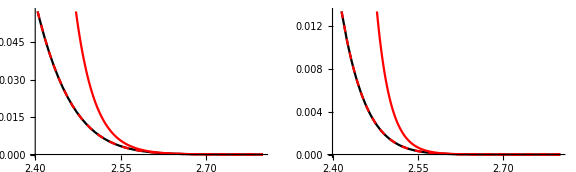

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{σH[R0[R],0,0],σHexp1[R,RR,0,0],σHexp2[R,RR,0,0]},{R,2.4,2.8},PlotStyle->{Black,Red,{Red,Dashed}}],
Plot[{σD[R0[R],0,0],σDexp1[R,RR,0,0],σDexp2[R,RR,0,0]},{R,2.4,2.8},PlotStyle->{Black,Red,{Red,Dashed}}]
},
ImageSize->Large]
```

## Morse overlap integrals in terms of the Wigner function based on [J. C. Lopez, A. L. Rivera, Yu. F. Smirnov, A. Frank, arXiv:physics/0109017v]

General case:

```mathematica
FCH[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],
{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

```mathematica
FCD[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`50;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

Case β_1=β_2:

```mathematica
FC0H[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)
(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCH instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

```mathematica
FC0D[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCD instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

## Morse overlap integrals and their distance dependence

### Numerical overlap integrals and attenuation parameters

```mathematica
SH[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1[x,i]ϕ2[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False]];
dSH[R_,i_,j_]:=Module[{h,S2M,SM,SP,S2P},
h=0.0001;
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
(S2M-8SM+8SP-S2P)/(12h)
];
```

```mathematica
SD[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1D[x,i]ϕ2D[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False]];
dSD[R_,i_,j_]:=Module[{h,S2M,SM,SP,S2P},
h=0.0001;
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
(S2M-8SM+8SP-S2P)/(12h)
];
```

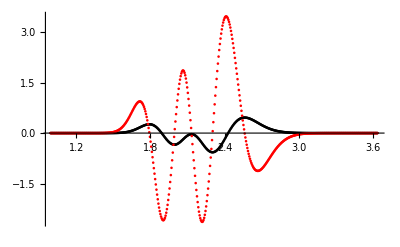

```mathematica
ListPlot[
{Table[{RDA[x],SH[x,1,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],dSH[x,1,3]},{x,-2.,3.,0.01}]},
PlotStyle->{Black,Red},
PlotRange->All
]
```

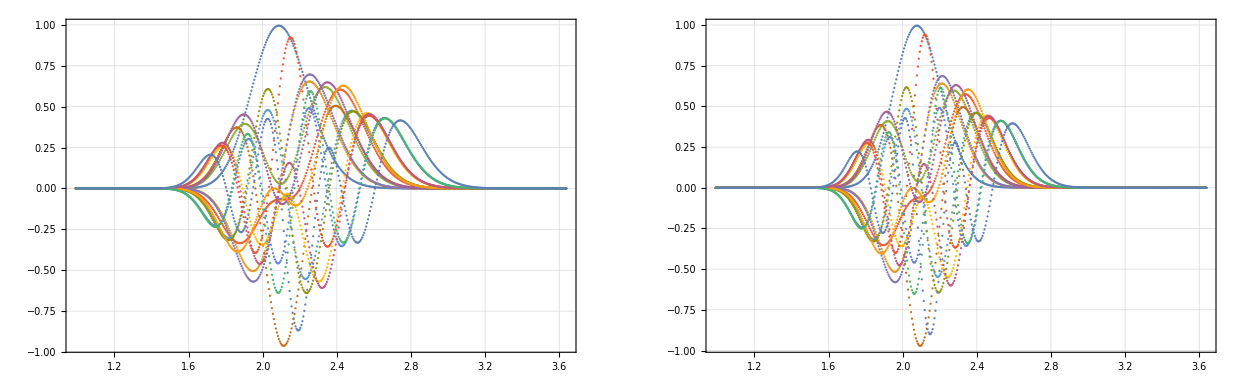

```mathematica
GraphicsRow[{
ListPlot[{
Table[{RDA[x],SH[x,0,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,3]},{x,-2.,3.,0.01}]
},
PlotRange->All,ImageSize->Large,PlotTheme->"Detailed"],
ListPlot[{
Table[{RDA[x],SD[x,0,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,3]},{x,-2.,3.,0.01}]
},
PlotRange->All,ImageSize->Large,PlotTheme->"Detailed"]
}]
```

```mathematica
{RDA[-2.0],RDA[4.0]}
```

{0.991646,4.16671}

```mathematica
sh=Interpolation[Table[{{x},SH[x,1,3]},{x,-2,3,0.01}],Method->"Spline",InterpolationOrder->3]
```

InterpolatingFunction[{{-2., 3.}}, <>]

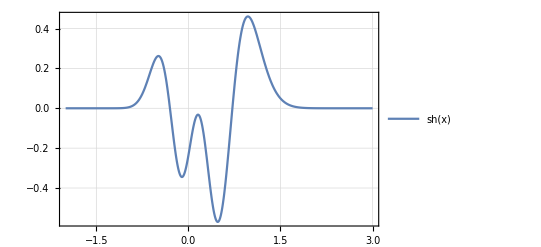

```mathematica
Plot[sh[x],{x,-2,3},PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
αH::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
αH4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γH::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γH4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
```

```mathematica
αD::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
αD4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γD::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γD4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
```

```mathematica
αH[R_,i_,j_]:=Module[{h,S0,SP,SM},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
SM=SH[R-h,i,j];
If[S0≤0,
(Message[αH::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(2h S0)(SP-SM),AccN]]
];
```

```mathematica
αH4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
If[S0≤0,
(Message[αH4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(12h S0)(-S2P+8SP-8SM+S2M),AccN]]
];
```

```mathematica
αD[R_,i_,j_]:=Module[{h,S0},
h=SetAccuracy[0.0001,AccN];
S0=SD[R,i,j];
If[S0≤0,
(Message[αD::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(2h S0)(SD[R+h,i,j]-SD[R-h,i,j]),AccN]]
];
```

```mathematica
αD4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M},
h=0.0001;
S0=SD[R,i,j];
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
If[S0≤0,
(Message[αD4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(12h S0)(-S2P+8SP-8SM+S2M),AccN]]
];
```

```mathematica
αH4[R0[2.5],0,2]
```

4.34562261648635939081941614858806133270263671875

```mathematica
Table[N[αH4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

9.14749835 | 7.80960917 | 6.39593806 | 4.8528198
7.78252133 | 6.14685052 | 4.2978439 | 1.94058239
6.31004264 | 4.19364992 | 1.53263722 | -3.14117891
4.67466223 | 1.58843657 | -3.55815058 | -130.270313

```mathematica
Table[N[αD4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

13.2977048 | 11.9856288 | 10.6247663 | 9.19194782
11.9567599 | 10.4643268 | 8.87641918 | 7.12592649
10.5464151 | 8.81001963 | 6.90131537 | 4.65499758
9.04462189 | 6.94884408 | 4.52172253 | 1.29022871

Coupling lengths for 0-0 overlap at equilibrium distance:

```mathematica
α0H[R_]:=αH4[R,0,0];
α0D[R_]:=αD4[R,0,0];
```

```mathematica
γH[R_,i_,j_]:=Module[{h,S0,dS,d2S},
h=SetAccuracy[0.0001,AccN];
S0=SH[R,i,j];
dS=(SH[R+h,i,j]-SH[R-h,i,j])/(2h);
d2S=(SH[R+h,i,j]-2S0+SH[R-h,i,j])/h^2;
If[S0≤0,
(Message[γH::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γH4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M,dS,d2S},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
dS=1/(12h)(S2M-8SM+8SP-S2P);
d2S=(-S2M+16SM-30S0+16SP-S2P)/(12 h^2);
If[S0≤0,
(Message[γH4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γD[R_,i_,j_]:=Module[{h,S0,dS,d2S},
h=SetAccuracy[0.0001,AccN];
S0=SD[R,i,j];
dS=(SD[R+h,i,j]-SD[R-h,i,j])/(2h);
d2S=(SD[R+h,i,j]-2S0+SD[R-h,i,j])/h^2;
If[S0≤0,
(Message[γD::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γD4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M,dS,d2S},
h=0.0001;
S0=SD[R,i,j];
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
dS=1/(12h)(S2M-8SM+8SP-S2P);
d2S=(-S2M+16SM-30S0+16SP-S2P)/(12 h^2);
If[S0≤0,
(Message[γD4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
Table[N[γH4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

6.81720697 | 7.80314895 | 8.85364354 | 10.1531463
7.81155338 | 9.79744392 | 12.5812144 | 18.2107289
9.00195163 | 12.9710094 | 20.3144151 | 48.7263585
10.6003142 | 20.106639 | 52.8929998 | 17044.0709

```mathematica
Table[N[γD4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

9.63664537 | 10.5865011 | 11.5668798 | 12.6540586
10.5859799 | 12.1160701 | 13.9000211 | 16.2895038
11.6509657 | 14.0644562 | 17.1970455 | 22.2195137
12.9112424 | 16.8608726 | 22.7895628 | 35.4758353

### Quality of expansions for harmonic overlaps:

```mathematica
SHexp1[R_,Req_,i_,j_]:=SH[R0[Req],i,j]Exp[-αH4[R0[Req],i,j](R0[R]-R0[Req])];
SHexp2[R_,Req_,i_,j_]:=SH[R0[Req],i,j]Exp[-αH4[R0[Req],i,j](R0[R]-R0[Req])-1/2 γH4[R0[Req],i,j](R0[R]-R0[Req])^2];
```

```mathematica
SDexp1[R_,Req_,i_,j_]:=SD[R0[Req],i,j]Exp[-αD4[R0[Req],i,j](R0[R]-R0[Req])];
SDexp2[R_,Req_,i_,j_]:=SD[R0[Req],i,j]Exp[-αD4[R0[Req],i,j](R0[R]-R0[Req])-1/2 γD4[R0[Req],i,j](R0[R]-R0[Req])^2];
```

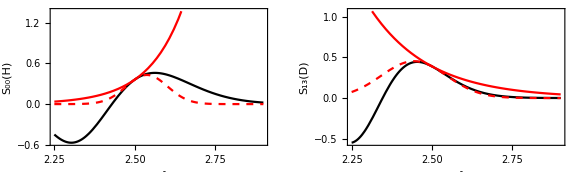

```mathematica
RR=2.5;
GraphicsRow[
{
Plot[{SH[R0[R],1,3],SHexp1[R,RR,1,3],SHexp2[R,RR,1,3]},{R,2.25,2.9},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_00(H)"}],
Plot[{SD[R0[R],1,3],SDexp1[R,RR,1,3],SDexp2[R,RR,1,3]},{R,2.25,2.9},
PlotStyle->{Black,Red,{Red,Dashed}},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_13(D)"}]
},
ImageSize->Large]
```

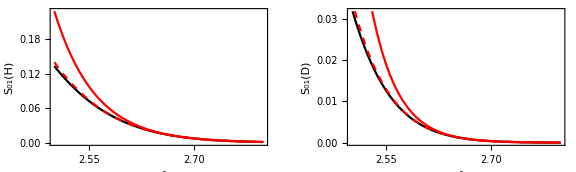

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{SH[R0[R],0,1],SHexp1[R,RR,0,1],SHexp2[R,RR,0,1]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_01(H)"}],
Plot[{SD[R0[R],0,1],SDexp1[R,RR,0,1],SDexp2[R,RR,0,1]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_01(D)"}]
},
ImageSize->Large]
```

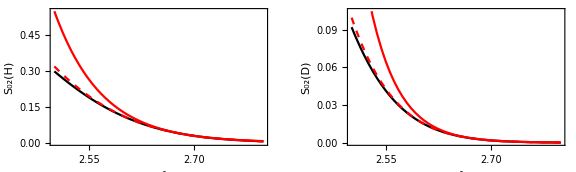

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{SH[R0[R],0,2],SHexp1[R,RR,0,2],SHexp2[R,RR,0,2]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_02(H)"}],
Plot[{SD[R0[R],0,2],SDexp1[R,RR,0,2],SDexp2[R,RR,0,2]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_02(D)"}]
},
ImageSize->Large]
```

### Spline all the distance dependencies

```mathematica
Clear[SHs,SHtable,SDs,SDtable,αHtable,αHs,γHtable,γHs]
```

```mathematica
Clear[αDtable,αDs,γDtable,γDs]
```

```mathematica
RDA[4.0]
```

4.16671

```mathematica
Nbound=3;
```

```mathematica
Array[SHs,{Nbound+1,Nbound+1},{0,0}];
Array[SHtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[SHtable[i,j]=ParallelTable[{Ri,SH[Ri,i,j]},{Ri,-3.0,4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[SHs[i,j]=Interpolation[SHtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}]
```

```mathematica
Array[αHs,{Nbound+1,Nbound+1},{0,0}];
Array[αHtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[αHtable[i,j]=ParallelTable[{Ri,αH4[Ri,i,j]},{Ri,R0[2.61],4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[αHs[i,j]=Interpolation[αHtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

```mathematica
Array[γHs,{Nbound+1,Nbound+1},{0,0}];
Array[γHtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[γHtable[i,j]=ParallelTable[{Ri,Re@γH4[Ri,i,j]},{Ri,R0[2.61],4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[γHs[i,j]=Interpolation[γHtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

```mathematica
Array[SDs,{Nbound+1,Nbound+1},{0,0}];
Array[SDtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[SDtable[i,j]=ParallelTable[{Ri,SD[Ri,i,j]},{Ri,-3.0,4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[SDs[i,j]=Interpolation[SDtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

```mathematica
Array[αDs,{Nbound+1,Nbound+1},{0,0}];
Array[αDtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[αDtable[i,j]=ParallelTable[{Ri,Re@αD4[Ri,i,j]},{Ri,R0[2.61],4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[αDs[i,j]=Interpolation[αDtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

```mathematica
Array[γDs,{Nbound+1,Nbound+1},{0,0}];
Array[γDtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[γDtable[i,j]=ParallelTable[{Ri,Re@γD4[Ri,i,j]},{Ri,R0[2.61],4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[γDs[i,j]=Interpolation[γDtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

### Coupling reorganization energies

```mathematica
λaH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2(αHs[i,j][R])^2)/(2μ Dalton),AccN]];
```

```mathematica
λaD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2(αDs[i,j][R])^2)/(2μ Dalton),AccN]];
```

```mathematica
λa0H=Function[{R,μ},SetAccuracy[(ℏ^2 α0H[R]^2)/(2μ Dalton),AccN]];
```

```mathematica
λa0D=Function[{R,μ},SetAccuracy[(ℏ^2 α0D[R]^2)/(2μ Dalton),AccN]];
```

```mathematica
λgH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γHs[i,j][R])/(2μ Dalton),AccN]];
```

```mathematica
λgD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γDs[i,j][R])/(2μ Dalton),AccN]];
```

## Partition function and Boltzmann factors

### Proton levels in a Morse potential

```mathematica
ZCH[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-(E1[i]-E1[0])/(kb T)],{i,1,n}],AccN]];
```

```mathematica
ZCD[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-(E1D[i]-E1D[0])/(kb T)],{i,1,n}],AccN]];
```

```mathematica
PCH=Function[{T,i,n},SetAccuracy[1/ZCH[T,n] Exp[-(E1[i]-E1[0])/(kb T)],AccN]];
```

```mathematica
PCD=Function[{T,i,n},SetAccuracy[1/ZCD[T,n] Exp[-(E1D[i]-E1D[0])/(kb T)],AccN]];
```

### Quantum (double adiabatic) R-mode

```mathematica
ZQCH[T_,Ω_,μmax_,mmax_]:=SetAccuracy[Sum[Exp[-(E1[μ]+ϵharm[m,Ω]-E1[0]-ϵharm[0,Ω])/(kb T)],{μ,0,μmax},{m,0,mmax}],AccN];
```

```mathematica
ZQCHe[T_,Ω_,μmax_]:=SetAccuracy[Exp[-(Ω cm2au)/(2 kb T)]/(1-Exp[-(Ω cm2au)/(kb T)])Sum[Exp[-(E1[μ]-E1[0])/(kb T)],{μ,0,μmax}],AccN];
```

```mathematica
ZQCD[T_,Ω_,μmax_,mmax_]:=SetAccuracy[Sum[Exp[-(E1D[μ]+ϵharm[m,Ω]-E1D[0]-ϵharm[0,Ω])/(kb T)],{μ,0,μmax},{m,0,mmax}],AccN];
```

```mathematica
ZQCDe[T_,Ω_,μmax_]:=SetAccuracy[Exp[-(Ω cm2au)/(2 kb T)]/(1-Exp[-(Ω cm2au)/(kb T)])Sum[Exp[-(E1D[μ]-E1D[0])/(kb T)],{μ,0,μmax}],AccN];
```

```mathematica
PQCH[T_,Ω_,μ_,m_,μmax_,mmax_]:=SetAccuracy[1/ZQCH[T,Ω,μmax,mmax] Exp[-(E1[μ]+ϵharm[m,Ω]-E1[0]-ϵharm[0,Ω])/(kb T)],AccN];
```

```mathematica
PQCHe[T_,Ω_,μ_,m_,μmax_]:=SetAccuracy[1/ZQCHe[T,Ω,μmax] Exp[-(E1[μ]+ϵharm[m,Ω]-E1[0])/(kb T)],AccN];
```

```mathematica
PQCD[T_,Ω_,μ_,m_,μmax_,mmax_]:=SetAccuracy[1/ZQCD[T,Ω,μmax,mmax] Exp[-(E1D[μ]+ϵharm[m,Ω]-E1D[0]-ϵharm[0,Ω])/(kb T)],AccN];
```

```mathematica
PQCDe[T_,Ω_,μ_,m_,μmax_]:=SetAccuracy[1/ZQCDe[T,Ω,μmax] Exp[-(E1D[μ]+ϵharm[m,Ω]-E1D[0])/(kb T)],AccN];
```

## Time Correlation Functions

#### Classical

```mathematica
CRC0=Function[{T,μ,ω},SetAccuracy[(kb T)/(μ Dalton (ω cm2au)^2),AccN]];
```

```mathematica
CRC=Function[{T,μ,ω,t},SetAccuracy[(kb T)/(μ Dalton (ω cm2au)^2)Cos[ω cm2au t],AccN]];
```

#### Quantum

```mathematica
CRQ0=Function[{T,μ,ω},SetAccuracy[ℏ^2/(2μ Dalton ω cm2au)Coth[(ω cm2au)/(2kb T)],AccN]];
```

```mathematica
CRQ=Function[{T,μ,ω,t},SetAccuracy[ℏ^2/(2μ Dalton ω cm2au)(Coth[(ω cm2au)/(2kb T)]Cos[(ω cm2au)/ℏ t]+ⅈ Sin[(ω cm2au)/ℏ t]),AccN]];
```

## Flux expressions (harmonic R-mode, short-time approximation)

### Full expressions from 10-th order cumulant expansion

Solvent damping term:

```mathematica
Sterm[λ_,T_,t_]:=SetAccuracy[Exp[-(λ*kcal2au*kb T t^2)/ℏ^2],AccN];
```

Coherent oscillatory term:

```mathematica
CItermH[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[ⅈ/ℏ((Δ+λ)*kcal2au+E2[j]-E2[0]-E1[i]+E1[0])t],AccN];
CItermD[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[ⅈ/ℏ((Δ+λ)*kcal2au+E2D[j]-E2D[0]-E1D[i]+E1D[0])t],AccN];
```

“Linear” R-terms (“black”, no quadratic term):

```mathematica
RblackH[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αHs[i,j][R])^2(CRQ[T,μ,ω,0]+CRQ[T,μ,ω,t])],AccN];
RblackD[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αDs[i,j][R])^2(CRQ[T,μ,ω,0]+CRQ[T,μ,ω,t])],AccN];
```

“Orange” term (1-st order in γ):

```mathematica
R1H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-γHs[i,j][R]CRQ[T,μ,ω,0]],AccN];
R1D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-γDs[i,j][R]CRQ[T,μ,ω,0]],AccN];
```

2-nd order in γ:

```mathematica
R2H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[1/2(γHs[i,j][R])^2(CRQ[T,μ,ω,0]^2+CRQ[T,μ,ω,t]^2)],AccN];
R2D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[1/2(γDs[i,j][R])^2(CRQ[T,μ,ω,0]^2+CRQ[T,μ,ω,t]^2)],AccN];
```

3-rd order in γ:

```mathematica
R3H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αHs[i,j][R])^2 γHs[i,j][R](CRQ[T,μ,ω,0]^2+CRQ[T,μ,ω,t]^2+2CRQ[T,μ,ω,0]CRQ[T,μ,ω,t])-1/3(γHs[i,j][R])^3(CRQ[T,μ,ω,0]^3+3CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^2)],AccN];
R3D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αDs[i,j][R])^2 γDs[i,j][R](CRQ[T,μ,ω,0]^2+CRQ[T,μ,ω,t]^2+2CRQ[T,μ,ω,0]CRQ[T,μ,ω,t])-1/3(γDs[i,j][R])^3(CRQ[T,μ,ω,0]^3+3CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^2)],AccN];
```

4-th order in γ:

```mathematica
R4H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αHs[i,j][R])^2(γHs[i,j][R])^2(CRQ[T,μ,ω,0]^3+CRQ[T,μ,ω,t]^3+3 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]+3CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^2)+1/4(γHs[i,j][R])^4(CRQ[T,μ,ω,0]^4+CRQ[T,μ,ω,t]^4+6 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^2)],AccN];
R4D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αDs[i,j][R])^2(γDs[i,j][R])^2(CRQ[T,μ,ω,0]^3+CRQ[T,μ,ω,t]^3+3 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]+3CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^2)+1/4(γDs[i,j][R])^4(CRQ[T,μ,ω,0]^4+CRQ[T,μ,ω,t]^4+6 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^2)],AccN];
```

5-th order in γ:

```mathematica
R5H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αHs[i,j][R])^2(γHs[i,j][R])^3(CRQ[T,μ,ω,0]^4+CRQ[T,μ,ω,t]^4+4 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]+4CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^3+6 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^2)-1/5(γHs[i,j][R])^5(CRQ[T,μ,ω,0]^5+5CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^4+10 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^2)],AccN];
R5D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αDs[i,j][R])^2(γDs[i,j][R])^3(CRQ[T,μ,ω,0]^4+CRQ[T,μ,ω,t]^4+4 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]+4CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^3+6 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^2)-1/5(γDs[i,j][R])^5(CRQ[T,μ,ω,0]^5+5CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^4+10 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^2)],AccN];
```

6-th order in γ:

```mathematica
R6H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αHs[i,j][R])^2(γHs[i,j][R])^4(CRQ[T,μ,ω,0]^5+CRQ[T,μ,ω,t]^5+5 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]+5CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^4+10 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^3+10 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^2)+1/6(γHs[i,j][R])^6(CRQ[T,μ,ω,0]^6+CRQ[T,μ,ω,t]^6+15 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^4+15 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^2)],AccN];
R6D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αDs[i,j][R])^2(γDs[i,j][R])^4(CRQ[T,μ,ω,0]^5+CRQ[T,μ,ω,t]^5+5 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]+5CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^4+10 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^3+10 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^2)+1/6(γDs[i,j][R])^6(CRQ[T,μ,ω,0]^6+CRQ[T,μ,ω,t]^6+15 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^4+15 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^2)],AccN];
```

7-th order in γ:

```mathematica
R7H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αHs[i,j][R])^2(γHs[i,j][R])^5(CRQ[T,μ,ω,0]^6+CRQ[T,μ,ω,t]^6+6 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]+6CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^5+15 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^4+15 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^2+20 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^3)-1/7(γHs[i,j][R])^7(CRQ[T,μ,ω,0]^7+21 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^2+35 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^4+7CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^6)],AccN];
R7D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(αDs[i,j][R])^2(γDs[i,j][R])^5(CRQ[T,μ,ω,0]^6+CRQ[T,μ,ω,t]^6+6 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]+6CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^5+15 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^4+15 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^2+20 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^3)-1/7(γDs[i,j][R])^7(CRQ[T,μ,ω,0]^7+21 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^2+35 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^4+7CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^6)],AccN];
```

8-th order in γ:

```mathematica
R8H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αHs[i,j][R])^2(γHs[i,j][R])^6(CRQ[T,μ,ω,0]^7+CRQ[T,μ,ω,t]^7+7 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]+7CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^6+21 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^5+21 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^2+35 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^4+35 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^3)+1/8(γHs[i,j][R])^8(CRQ[T,μ,ω,0]^8+CRQ[T,μ,ω,t]^8+28 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^6+28 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^2+70 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^4)],AccN];
R8D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(αDs[i,j][R])^2(γDs[i,j][R])^6(CRQ[T,μ,ω,0]^7+CRQ[T,μ,ω,t]^7+7 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]+7CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^6+21 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^5+21 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^2+35 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^4+35 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^3)+1/8(γDs[i,j][R])^8(CRQ[T,μ,ω,0]^8+CRQ[T,μ,ω,t]^8+28 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^6+28 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^2+70 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^4)],AccN];
```

9-th order in γ:

```mathematica
R9H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(CRQ[T,μ,ω,0]^8+8 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]+28 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^2+56 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^3+70 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^4+56 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^5+28 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^6+8 CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^7+CRQ[T,μ,ω,t]^8) (αHs[i,j][R])^2 (γHs[i,j][R])^7-(1/9 CRQ[T,μ,ω,0]^9+4 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]^2+14 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^4+28/3 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^6+CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^8) (γHs[i,j][R])^9],AccN];
R9D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[-(CRQ[T,μ,ω,0]^8+8 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]+28 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^2+56 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^3+70 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^4+56 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^5+28 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^6+8 CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^7+CRQ[T,μ,ω,t]^8) (αDs[i,j][R])^2 (γDs[i,j][R])^7-(1/9 CRQ[T,μ,ω,0]^9+4 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]^2+14 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^4+28/3 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^6+CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^8) (γDs[i,j][R])^9],AccN];
```

10-th order in γ:

```mathematica
R10H[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(CRQ[T,μ,ω,0]^9+9 CRQ[T,μ,ω,0]^8 CRQ[T,μ,ω,t]+36 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]^2+84 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^3+126 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^4+126 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^5+84 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^6+36 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^7+9 CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^8+CRQ[T,μ,ω,t]^9) (αHs[i,j][R])^2 (γHs[i,j][R])^8+(1/10 CRQ[T,μ,ω,0]^10+9/2 CRQ[T,μ,ω,0]^8 CRQ[T,μ,ω,t]^2+21 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^4+21 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^6+9/2 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^8+1/10 CRQ[T,μ,ω,t]^10) (γHs[i,j][R])^10],AccN];
R10D[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[(CRQ[T,μ,ω,0]^9+9 CRQ[T,μ,ω,0]^8 CRQ[T,μ,ω,t]+36 CRQ[T,μ,ω,0]^7 CRQ[T,μ,ω,t]^2+84 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^3+126 CRQ[T,μ,ω,0]^5 CRQ[T,μ,ω,t]^4+126 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^5+84 CRQ[T,μ,ω,0]^3 CRQ[T,μ,ω,t]^6+36 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^7+9 CRQ[T,μ,ω,0] CRQ[T,μ,ω,t]^8+CRQ[T,μ,ω,t]^9) (αDs[i,j][R])^2 (γDs[i,j][R])^8+(1/10 CRQ[T,μ,ω,0]^10+9/2 CRQ[T,μ,ω,0]^8 CRQ[T,μ,ω,t]^2+21 CRQ[T,μ,ω,0]^6 CRQ[T,μ,ω,t]^4+21 CRQ[T,μ,ω,0]^4 CRQ[T,μ,ω,t]^6+9/2 CRQ[T,μ,ω,0]^2 CRQ[T,μ,ω,t]^8+1/10 CRQ[T,μ,ω,t]^10) (γDs[i,j][R])^10],AccN];
```

Complex Flux:

```mathematica
q0fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t];
q0fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t];
```

```mathematica
q1fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t];
q1fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t];
```

```mathematica
q2fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t];
q2fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t];
```

```mathematica
q3fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t];
q3fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t];
```

```mathematica
q4fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t];
q4fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t];
```

```mathematica
q5fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t];
q5fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t];
```

```mathematica
q6fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t]R6H[T,R,μ,ω,i,j,t];
q6fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t]R6D[T,R,μ,ω,i,j,t];
```

```mathematica
q7fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t]R6H[T,R,μ,ω,i,j,t]R7H[T,R,μ,ω,i,j,t];
q7fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t]R6D[T,R,μ,ω,i,j,t]R7D[T,R,μ,ω,i,j,t];
```

```mathematica
q8fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t]R6H[T,R,μ,ω,i,j,t]R7H[T,R,μ,ω,i,j,t]R8H[T,R,μ,ω,i,j,t];
q8fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t]R6D[T,R,μ,ω,i,j,t]R7D[T,R,μ,ω,i,j,t]R8D[T,R,μ,ω,i,j,t];
```

```mathematica
q9fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t]R6H[T,R,μ,ω,i,j,t]R7H[T,R,μ,ω,i,j,t]R8H[T,R,μ,ω,i,j,t]R9H[T,R,μ,ω,i,j,t];
q9fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t]R6D[T,R,μ,ω,i,j,t]R7D[T,R,μ,ω,i,j,t]R8D[T,R,μ,ω,i,j,t]R9D[T,R,μ,ω,i,j,t];
```

```mathematica
q10fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermH[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackH[T,R,μ,ω,i,j,t]R1H[T,R,μ,ω,i,j,t]R2H[T,R,μ,ω,i,j,t]R3H[T,R,μ,ω,i,j,t]R4H[T,R,μ,ω,i,j,t]R5H[T,R,μ,ω,i,j,t]R6H[T,R,μ,ω,i,j,t]R7H[T,R,μ,ω,i,j,t]R8H[T,R,μ,ω,i,j,t]R9H[T,R,μ,ω,i,j,t]R10H[T,R,μ,ω,i,j,t];
q10fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=CItermD[Δ,λ,R,μ,ω,i,j,t]Sterm[λ,T,t]RblackD[T,R,μ,ω,i,j,t]R1D[T,R,μ,ω,i,j,t]R2D[T,R,μ,ω,i,j,t]R3D[T,R,μ,ω,i,j,t]R4D[T,R,μ,ω,i,j,t]R5D[T,R,μ,ω,i,j,t]R6D[T,R,μ,ω,i,j,t]R7D[T,R,μ,ω,i,j,t]R8D[T,R,μ,ω,i,j,t]R9D[T,R,μ,ω,i,j,t]R10D[T,R,μ,ω,i,j,t];
```

### Some test flux calculations

```mathematica
TT=300;
ΩΩ=200;
MM=10;
R0au=R0[2.8];
ΔΔ=0;
λλ=ev2au*au2kcal;
```

```mathematica
q0NH=Re[q0fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q1NH=Re[q1fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q2NH=Re[q2fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q3NH=Re[q3fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q4NH=Re[q4fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q5NH=Re[q5fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q6NH=Re[q6fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q7NH=Re[q7fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q8NH=Re[q8fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q9NH=Re[q9fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
q10NH=Re[q10fluxH[TT,ΔΔ,λλ,R0au,MM,ΩΩ,0,0,0]]
```

3.5986047629091791808605194091796875×10^7

2.480717043267355717507060202501217369898970028022×10^7

2.848893217766972241091679367711441495598994319495×10^7

63.551415828493642425412527681513756842430816

1.0053524972510362633829662419793622781330535×10^6

759.63651352178535889879057367181245087894256

159192.76501567261781588415337530546345920795

2988.9744331421267519458468995819989521878903

57490.438590437767282430152710114957262979548

6374.6941985656973043715564026460048152358874

32730.497005189986804574630356139747334781091

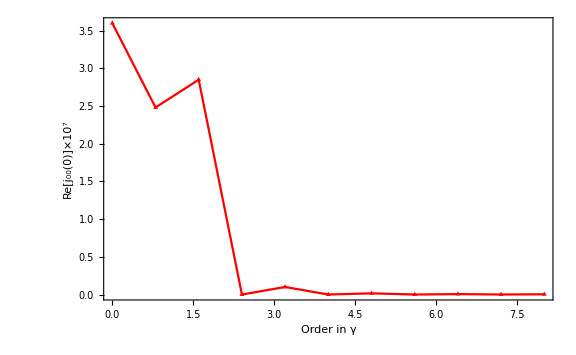

```mathematica
ListLinePlot[10^-7{q0NH,q1NH,q2NH,q3NH,q4NH,q5NH,q6NH,q7NH,q8NH,q9NH,q10NH},DataRange->{0,8},
Axes->False,Frame->True,FrameLabel->{"Order in γ","Re[j_00(0)]×10^7"},PlotStyle->Red,
ImageSize->Large,BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotMarkers->▲]
```

Real parts of the normalized flux:

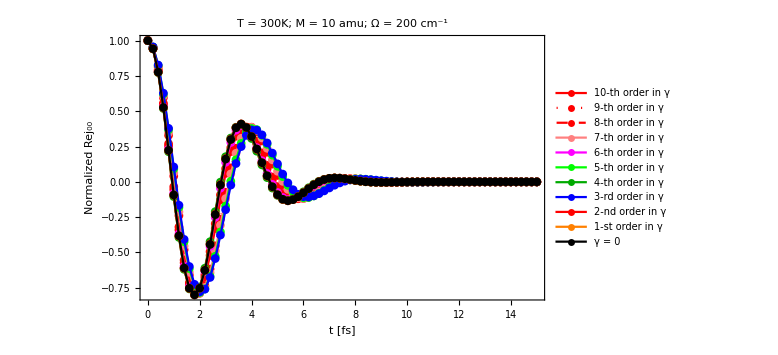

```mathematica
Show[
ListLinePlot[Table[{t,Re[q10fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q10NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Red,PlotLegends->{"10-th order in γ"}],
ListLinePlot[Table[{t,Re[q9fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q9NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->{Red,Dotted},PlotLegends->{"9-th order in γ"}],
ListLinePlot[Table[{t,Re[q8fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q8NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->{Red,Dashed},PlotLegends->{"8-th order in γ"}],
ListLinePlot[Table[{t,Re[q7fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q7NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Pink,PlotLegends->{"7-th order in γ"}],
ListLinePlot[Table[{t,Re[q6fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q6NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Magenta,PlotLegends->{"6-th order in γ"}],
ListLinePlot[Table[{t,Re[q5fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q5NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Green,PlotLegends->{"5-th order in γ"}],
ListLinePlot[Table[{t,Re[q4fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q4NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Darker[Green],PlotLegends->{"4-th order in γ"}],
ListLinePlot[Table[{t,Re[q3fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q3NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Blue,PlotLegends->{"3-rd order in γ"}],
ListLinePlot[Table[{t,Re[q2fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q2NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Red,PlotLegends->{"2-nd order in γ"}],
ListLinePlot[Table[{t,Re[q1fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q1NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Orange,PlotLegends->{"1-st order in γ"}],
ListLinePlot[Table[{t,Re[q0fluxH[TT,Δ,λ,R0au,MM,Ω,0,0,t/(1000 au2ps)]]/q0NH},{t,0,15,0.2}],
PlotRange->All,PlotMarkers->Automatic,PlotStyle->Black,PlotLegends->{"γ = 0"}],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Axes->False,Frame->True,FrameLabel->{"t [fs]","Normalized Rej_00"},
ImageSize->Large,PlotRange->All,
PlotLabel->"T = "<>ToString[TT]<>"K; M = "<>ToString[MM]<>" amu; Ω = "<>ToString[Ω]<>" cm^-1"]
```

### Expressions for linear exponential coupling (no quadratic terms)

Solvent damping term:

```mathematica
Sterm[λ_,T_,t_]:=SetAccuracy[Exp[-(λ*kcal2au*kb T t^2)/ℏ^2],AccN];
```

Coherent oscillatory term:

```mathematica
CtermH[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2[j]-E2[0]-E1[i]+E1[0])t+λaH[R,μ,i,j]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
CtermD[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2D[j]-E2D[0]-E1D[i]+E1D[0])t+λaD[R,μ,i,j]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
```

```mathematica
C0termH[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2[j]-E2[0]-E1[i]+E1[0])t+λa0H[R,μ]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
C0termD[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2D[j]-E2D[0]-E1D[i]+E1D[0])t+λa0D[R,μ]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
```

R-mode term:

```mathematica
RtermH[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[λaH[R,μ,i,j]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
RtermD[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[λaD[R,μ,i,j]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
```

```mathematica
R0termH[T_,R_,μ_,ω_,t_]:=SetAccuracy[Exp[λa0H[R,μ]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
R0termD[T_,R_,μ_,ω_,t_]:=SetAccuracy[Exp[λa0D[R,μ]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
```

And now, real part of the total flux:

```mathematica
ReqfluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]CtermH[Δ,λ,R,μ,ω,i,j,t]RtermH[T,R,μ,ω,i,j,t];
ReqfluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]CtermD[Δ,λ,R,μ,ω,i,j,t]RtermD[T,R,μ,ω,i,j,t];
```

```mathematica
Reqflux0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]C0termH[Δ,λ,R,μ,ω,i,j,t]R0termH[T,R,μ,ω,t];
Reqflux0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]C0termD[Δ,λ,R,μ,ω,i,j,t]R0termD[T,R,μ,ω,t];
```

## Exact (flux) rate constants

### Rates with only linear terms in the coupling

```mathematica
RateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=CtermH[Δ,λ,R,μ,ω,i,j,t];
rterm0=RtermH[T,R,μ,ω,i,j,0];
rterm=RtermH[T,R,μ,ω,i,j,t];
reflux=sterm*cterm*rterm/rterm0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
Rateqflux0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=C0termH[Δ,λ,R,μ,ω,i,j,t];
rterm0=R0termH[T,R,μ,ω,0];
rterm=R0termH[T,R,μ,ω,t];
reflux=sterm*cterm*rterm/rterm0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
RateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=CtermD[Δ,λ,R,μ,ω,i,j,t];
rterm0=RtermD[T,R,μ,ω,i,j,0];
rterm=RtermD[T,R,μ,ω,i,j,t];
reflux=sterm*cterm*rterm/rterm0;
s2=Abs[SDs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
Rateqflux0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=C0termD[Δ,λ,R,μ,ω,i,j,t];
rterm0=R0termD[T,R,μ,ω,0];
rterm=R0termD[T,R,μ,ω,t];
reflux=sterm*cterm*rterm/rterm0;
s2=Abs[SDs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*s2*rterm0*fluxint];
```

```mathematica
TotalrateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCH[T,i,n]Sum[RateqfluxH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCD[T,i,n]Sum[RateqfluxD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrateqflux0H[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCH[T,i,n]Sum[Rateqflux0H[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrateqflux0D[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCD[T,i,n]Sum[Rateqflux0D[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEqflux=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m]/TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIEqflux0=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrateqflux0H[T,Δ,λ,R,μ,ω,n,m]/Totalrateqflux0D[T,Δ,λ,R,μ,ω,n,m]];
```

### Rates with linear and quadratic terms in the coupling

```mathematica
Rateq0fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q0fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q0fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq1fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q1fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q1fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq2fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q2fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q2fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq3fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q3fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q3fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq4fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q4fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q4fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq5fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q5fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q5fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq6fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q6fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q6fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq7fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q7fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q7fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq8fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q8fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q8fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq9fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q9fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q9fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Rateq10fluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q10fluxH[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q10fluxH[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SHs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
Rateq10fluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{prefactor,t,flux,flux0,reflux,s2,fluxint},
prefactor=SetAccuracy[10^12/au2ps,AccN];
flux=q10fluxD[T,Δ,λ,R,μ,ω,i,j,t];
flux0=Re[q10fluxD[T,Δ,λ,R,μ,ω,i,j,0]];
reflux=Re[flux]/flux0;
s2=Abs[SDs[i,j][R]]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->30];
2*prefactor*V^2*s2*flux0*fluxint];
```

```mathematica
Totalrateq10fluxH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCH[T,i,n]Sum[Rateq10fluxH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrateq10fluxD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCD[T,i,n]Sum[Rateq10fluxD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEq10flux=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrateq10fluxH[T,Δ,λ,R,μ,ω,n,m]/Totalrateq10fluxD[T,Δ,λ,R,μ,ω,n,m]];
```

## Quantum (double adiabatic) rate constants

```mathematica
n=10;{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,AccN];
```

```mathematica
FWDAQH[R_,M_,Ω_,μ_,m_,ν_,n_]:=
Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=SHs[μ,ν][x]ψharm[x,R,M,Ω,m]ψharm[x,R,M,Ω,n];
a=-2;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]]

(*Print["Interval: [",a,",",b,"]=>  Integral = ",integral,"  Error = ",error]*)
];
integral];
FWDAQD[R_,M_,Ω_,μ_,m_,ν_,n_]:=
Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=SDs[μ,ν][x]ψharm[x,R,M,Ω,m]ψharm[x,R,M,Ω,n];
a=-2;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]]

(*Print["Interval: [",a,",",b,"]=>  Integral = ",integral,"  Error = ",error]*)
];
integral];
```

```mathematica
partialRateDAQH[T_,Δ_,λ_,R_,M_,Ω_,μ_,m_,ν_,n_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWDAQH[R,M,Ω,μ,m,ν,n];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[ν]-E2[0]-E1[μ]+E1[0]+ϵharm[n,Ω]-ϵharm[m,Ω])^2/(4Λ);
A0*A1^2*A2*Exp[-Ea/(kb T)]];
partialRateDAQD[T_,Δ_,λ_,R_,M_,Ω_,μ_,m_,ν_,n_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWDAQD[R,M,Ω,μ,m,ν,n];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[ν]-E2D[0]-E1D[μ]+E1D[0]+ϵharm[n,Ω]-ϵharm[m,Ω])^2/(4Λ);
A0*A1^2*A2*Exp[-Ea/(kb T)]];
```

```mathematica
totalRateDAQH[T_,Δ_,λ_,R_,M_,Ω_,μmax_,mmax_,νmax_,nmax_]:=Sum[PQCHe[T,Ω,μ,m,μmax]Sum[partialRateDAQH[T,Δ,λ,R,M,Ω,μ,m,ν,n],{ν,0,νmax},{n,0,nmax}],{μ,0,μmax},{m,0,mmax}];
totalRateDAQD[T_,Δ_,λ_,R_,M_,Ω_,μmax_,mmax_,νmax_,nmax_]:=Sum[PQCDe[T,Ω,μ,m,μmax]Sum[partialRateDAQD[T,Δ,λ,R,M,Ω,μ,m,ν,n],{ν,0,νmax},{n,0,nmax}],{μ,0,μmax},{m,0,mmax}];
```

```mathematica
KIEDAQ=Function[{T,Δ,λ,R,μ,ω,μmax,mmax,νmax,nmax},totalRateDAQH[T,Δ,λ,R,μ,ω,μmax,mmax,νmax,nmax]/totalRateDAQD[T,Δ,λ,R,μ,ω,μmax,mmax,νmax,nmax]];
```

## Aproximate rate expressions

```mathematica
RateH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,ζ,A1,A2,λα,λγ,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
ζ=Coth[(ω cm2au)/(2 kb T)];
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[(2λα ζ)/(ω cm2au)];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,ζ,A1,A2,λα,λγ,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
ζ=Coth[(ω cm2au)/(2 kb T)];
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[(2λα ζ)/(ω cm2au)];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIE=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH[T,Δ,λ,R,μ,ω,n,m]/TotalrateD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
RateHg[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,ζ,A11,A12,A2,λα,λγ,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
λγ=λgH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
ζ=Coth[(ω cm2au)/(2 kb T)];
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A11=Exp[(2λα ζ)/(ω cm2au+2λγ ζ)];
A12=(1+(2λγ ζ)/(ω cm2au))^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A11*A12*A2*Exp[-Ea/(kb T)]];
RateDg[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,ζ,A11,A12,A2,λα,λγ,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
λγ=λgD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
ζ=Coth[(ω cm2au)/(2 kb T)];
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A11=Exp[(2λα ζ)/(ω cm2au+2λγ ζ)];
A12=(1+(2λγ ζ)/(ω cm2au))^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A11*A12*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateHg[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateHg[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateDg[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateDg[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEg=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateHg[T,Δ,λ,R,μ,ω,n,m]/TotalrateDg[T,Δ,λ,R,μ,ω,n,m]];
```

### High-T Approximation for R-mode (Eq. 6)

```mathematica
RateH6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateH6g[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
λγ=λgH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A11=Exp[(4kb T*λα)/(ω cm2au)^2];
A12=Exp[-(16kb T*kb T*λα*λγ)/((ω cm2au)^2((ω cm2au)^2+4λγ kb T))];
A13=(1+(4λγ kb T)/(ω cm2au)^2)^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0H6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateD6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateD6g[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
λγ=λgD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A11=Exp[(4kb T*λα)/(ω cm2au)^2];
A12=Exp[-(16kb T*kb T*λα*λγ)/((ω cm2au)^2((ω cm2au)^2+4λγ kb T))];
A13=(1+(4λγ kb T)/(ω cm2au)^2)^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0D6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateH6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateH6g[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH6g[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateD6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateD6g[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD6g[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0H6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Rate0H6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0D6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Rate0D6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIE6=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH6[T,Δ,λ,R,μ,ω,n,m]/TotalrateD6[T,Δ,λ,R,μ,ω,n,m]];
KIE6g=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH6g[T,Δ,λ,R,μ,ω,n,m]/TotalrateD6g[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIE06=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrate0H6[T,Δ,λ,R,μ,ω,n,m]/Totalrate0D6[T,Δ,λ,R,μ,ω,n,m]];
```

### Simplified High-T Approximation (Eq. 7)

```mathematica
RateH7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateH7g[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
λγ=λgH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A11=Exp[(4kb T*λα)/(ω cm2au)^2];
A12=Exp[-(16kb T*kb T*λα*λγ)/((ω cm2au)^2((ω cm2au)^2+4λγ kb T))];
A13=(1+(4λγ kb T)/(ω cm2au)^2)^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0H7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateD7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateD7g[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
λγ=λgD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A11=Exp[(4kb T*λα)/(ω cm2au)^2];
A12=Exp[-(16kb T*kb T*λα*λγ)/((ω cm2au)^2((ω cm2au)^2+4λγ kb T))];
A13=(1+(4λγ kb T)/(ω cm2au)^2)^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0D7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateH7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateH7g[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH7g[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateD7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateD7g[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD7g[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0H7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Rate0H7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0D7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Rate0D7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIE7=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH7[T,Δ,λ,R,μ,ω,n,m]/TotalrateD7[T,Δ,λ,R,μ,ω,n,m]];
KIE7g=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH7g[T,Δ,λ,R,μ,ω,n,m]/TotalrateD7g[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIE07=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrate0H7[T,Δ,λ,R,μ,ω,n,m]/Totalrate0D7[T,Δ,λ,R,μ,ω,n,m]];
```

### Low-T approximation

```mathematica
RatelowH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RatelowHg[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
λγ=λgH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A11=Exp[(2λα)/(ω cm2au)];
A12=Exp[-(4λα λγ)/((ω cm2au)^2(1+(2λγ)/(ω cm2au)))];
A13=(1+(2λγ)/(ω cm2au))^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Ratelow0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SHs[i,j][R]]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RatelowD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RatelowDg[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A11,A12,A13,A2,λα,λγ,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
λγ=λgD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A11=Exp[(2λα)/(ω cm2au)];
A12=Exp[-(4λα λγ)/((ω cm2au)^2(1+(2λγ)/(ω cm2au)))];
A13=(1+(2λγ)/(ω cm2au))^(-1/2);
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A11*A12*A13*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Ratelow0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*Abs[SDs[i,j][R]]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalratelowH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RatelowH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalratelowHg[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RatelowHg[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalratelowD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RatelowD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalratelowDg[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RatelowDg[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalratelow0H[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Ratelow0H[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalratelow0D[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Ratelow0D[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIElowT=Function[{T,Δ,λ,R,μ,ω,n,m},TotalratelowH[T,Δ,λ,R,μ,ω,n,m]/TotalratelowD[T,Δ,λ,R,μ,ω,n,m]];
KIElowTg=Function[{T,Δ,λ,R,μ,ω,n,m},TotalratelowHg[T,Δ,λ,R,μ,ω,n,m]/TotalratelowDg[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIElow0T=Function[{T,Δ,λ,R,μ,ω,n,m},Totalratelow0H[T,Δ,λ,R,μ,ω,n,m]/Totalratelow0D[T,Δ,λ,R,μ,ω,n,m]];
```

## Averaging of overlap integral (a la Ulstrup-Kuznetsov)

Quantum and classical distribution functions for harmonic R-oscillator:

```mathematica
PQ[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton ω cm2au)/(π ℏ^2)Tanh[(ω cm2au)/(2kb T)])Exp[-(μ Dalton ω cm2au)/ℏ^2 Tanh[(ω cm2au)/(2kb T)](x-R)^2],AccN];
```

```mathematica
PC[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton (ω cm2au)^2)/(2π kb T))Exp[-1/(2kb T)μ Dalton (ω cm2au)^2(x-R)^2],AccN];
```

Averaged (actual) Franck-Condon factors:

```mathematica
n=10;{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,AccN];
```

```mathematica
FWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SHs[i,j][x]]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

```mathematica
FWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SDs[i,j][x]]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;
(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};
(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};
(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];
(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];
];
integral];
```

Averaged (quadratic expansion) Franck-Condon factors:

```mathematica
LFWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SHs[i,j][x0]]^2 Exp[-2αH[x0,i,j](x-x0)]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
QFWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SHs[i,j][x0]]^2 Exp[-2αH[x0,i,j](x-x0)-γH[x0,i,j](x-x0)^2]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

```mathematica
LFWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SDs[i,j][x0]]^2 Exp[-2αD[x0,i,j](x-x0)]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
QFWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SDs[i,j][x0]]^2 Exp[-2αD[x0,i,j](x-x0)-γD[x0,i,j](x-x0)^2]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

### Rates:

```mathematica
RateUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateQUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateQUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateLUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateQUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateQUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateLUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIEQUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKqD[T,Δ,λ,R,μ,ω,n,m]];
KIELUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKqD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
RateUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateQUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateQUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateLUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateQUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateQUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateLUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKD[T,Δ,λ,R,μ,ω,n,m]];
KIEQUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKD[T,Δ,λ,R,μ,ω,n,m]];
KIELUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateLUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateLUKD[T,Δ,λ,R,μ,ω,n,m]];
```

## Fixed R

```mathematica
RateRH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=Abs[SHs[i,j][R]]^2;
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateRD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=Abs[SDs[i,j][R]]^2;
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateRH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateRH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateRD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateRD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIERT=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateRH[T,Δ,λ,R,μ,ω,n,m]/TotalrateRD[T,Δ,λ,R,μ,ω,n,m]];
```

## Rate channel contributions

#### Rate matrices (contributions for all channels organized into matrices)

```mathematica
rateqfluxHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateqfluxH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateqfluxDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateqfluxD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateH6matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateH6[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateH6[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateD6matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateD6[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateD6[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateH7matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateH7[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateH7[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateD7matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateD7[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateD7[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
ratelowHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalratelowH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RatelowH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
ratelowDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalratelowD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RatelowD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateUKH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateUKD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKqHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateUKqH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKqDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateUKqD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateRHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateRH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateRH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateRDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateRD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateRD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

#### Rate analysis tables

```mathematica
headings={"i","j","ΔG_ij^o","ΔG_ij^≠","S_ij^2","exp[-βΔG_ij^≠]","%"};
```

```mathematica
tablerateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateqfluxH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateqfluxD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateH6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateH6[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateH6[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateD6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateD6[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateD6[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateH6[303,-4.5,13.4,R0[2.77],100,132,2,2]
```

(H):    λ=13.4kcal/mol; R_0=2.77Å; M=100amu; Ω=132cm^-1 |  |  |  |  |  | 
i | j | ΔG_ij^o | ΔG_ij^≠ | S_ij^2 | exp[-βΔG_ij^≠] | %
0 | 0 | -4.5 | 1.478 | 1.08519×10^-7 | 8.59234×10^-2 | 98.76
0 | 1 | 3.03 | 5.036 | 4.53508×10^-6 | 2.33129×10^-4 | 1.078
0 | 2 | 10.15 | 10.35 | 9.38882×10^-5 | 3.44225×10^-8 | 0.00009621
1 | 0 | -13.6 | 0.0007742 | 5.5495×10^-6 | 9.98715×10^-1 | 0.1096
1 | 1 | -6.074 | 1.001 | 1.49271×10^-4 | 1.89573×10^-1 | 0.05187
1 | 2 | 1.047 | 3.894 | 1.93494×10^-3 | 1.55453×10^-3 | 0.0001522
2 | 0 | -22.14 | 1.424 | 1.30168×10^-4 | 9.39423×10^-2 | 3.994×10^-6
2 | 1 | -14.61 | 0.02718 | 2.18064×10^-3 | 9.55866×10^-1 | 0.00006406
2 | 2 | -7.486 | 0.6524 | 1.70525×10^-2 | 3.384×10^-1 | 4.92×10^-6

```mathematica
tablerateD6[303,-5,20,R0[2.7],100,200,1,1]
```

(D):    λ=20kcal/mol; R_0=2.7Å; M=100amu; Ω=200cm^-1 |  |  |  |  |  | 
i | j | ΔG_ij^o | ΔG_ij^≠ | S_ij^2 | exp[-βΔG_ij^≠] | %
0 | 0 | -5. | 2.813 | 3.27137×10^-9 | 9.36341×10^-3 | 74.81
0 | 1 | 0.4104 | 5.207 | 1.49913×10^-7 | 1.75444×10^-4 | 15.72
1 | 0 | -11.56 | 0.891 | 1.85785×10^-7 | 2.27677×10^-1 | 5.74
1 | 1 | -6.147 | 2.399 | 6.14797×10^-6 | 1.86089×10^-2 | 3.723

```mathematica
tablerateH7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateH7[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateH7[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateD7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateD7[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateD7[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tableratelowH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalratelowH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RatelowH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tableratelowD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalratelowD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RatelowD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateUKH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateUKD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SHs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateUKqH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=Abs[SDs[i,j][R]]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateUKqD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

## Experimental data for SLO WT and its mutants

```mathematica
ratesHWT={
{1000/3.5971,213.35},
{1000/3.5336,228.94},
{1000/3.4722,269.96},
{1000/3.4130,275.10},
{1000/3.3557,327.19},
{1000/3.3003,297.11},
{1000/3.2468,329.06},
{1000/3.1949,301.77},
{1000/3.1447,348.08},
{1000/3.0960,327.51}
};
ratesHWTR=Table[{1000/ratesHWT⟦i,1⟧,Log[ratesHWT⟦i,2⟧]},{i,1,Length[ratesHWT]}];
ratesHWTRlg=Table[{1000/ratesHWT⟦i,1⟧,Log10[ratesHWT⟦i,2⟧]},{i,1,Length[ratesHWT]}];
```

```mathematica
ratesDWT={
{1000/3.5971,2.161},
{1000/3.5336,2.4767},
{1000/3.4722,2.9864},
{1000/3.3557,4.2919},
{1000/3.3003,3.6822},
{1000/3.2468,5.023},
{1000/3.1949,4.2442},
{1000/3.1447,4.0017}
};
ratesDWTR=Table[{1000/ratesDWT⟦i,1⟧,Log[ratesDWT⟦i,2⟧]},{i,1,Length[ratesDWT]}];
ratesDWTRlg=Table[{1000/ratesDWT⟦i,1⟧,Log10[ratesDWT⟦i,2⟧]},{i,1,Length[ratesDWT]}];
```

```mathematica
FindFit[ratesHWTR,A -Ea/(1000 kb au2kcal)x,{A,Ea},x]
```

{A→8.54005,Ea→1.71314}

```mathematica
FindFit[ratesHWTR,A -(-5.4+lambda)^2/(4 lambda 1000 kb au2kcal)x,{{A,8},{lambda,20}},x]
```

{A→8.54005,lambda→15.8079}

```mathematica
FindFit[ratesDWTR,A -(-5.4+lambda)^2/(4 lambda 1000 kb au2kcal)x,{{A,8},{lambda,20}},x]
```

{A→6.54083,lambda→22.0148}

KIE data for WT and i553 mutants:

```mathematica
KIEWT= {{278,98.727},{283,92.438},{288,90.396},{ 298,76.234},{ 303,80.688},{ 308,65.511},{ 313,71.102}}; 
KIEWTR=Table[{1000/KIEWT⟦i,1⟧,KIEWT⟦i,2⟧},{i,1,Length[KIEWT]}];
lnKIEWTR=Table[{1000/KIEWT⟦i,1⟧,Log[KIEWT⟦i,2⟧]},{i,1,Length[KIEWT]}];
lgKIEWTR=Table[{1000/KIEWT⟦i,1⟧,Log10[KIEWT⟦i,2⟧]},{i,1,Length[KIEWT]}];
```

```mathematica
KIEi553v = {{283,122.45},{288,100}, {293,106.49}, {298,84},{ 303,77.778},{ 308,78.261},{ 313,80.357},{ 318,72.857},{323,63.793}}; 
KIEi553vR=Table[{1000/KIEi553v⟦i,1⟧,KIEi553v⟦i,2⟧},{i,1,Length[KIEi553v]}];
lnKIEi553vR=Table[{1000/KIEi553v⟦i,1⟧,Log[KIEi553v⟦i,2⟧]},{i,1,Length[KIEi553v]}];
lgKIEi553vR=Table[{1000/KIEi553v⟦i,1⟧,Log10[KIEi553v⟦i,2⟧]},{i,1,Length[KIEi553v]}];
```

```mathematica
KIEi553l = {{283,127.2},{288,133.6},{ 293,88.889},{ 298,117.27},{ 303,80.294},{ 308,87.949},{ 313,78.14},{ 318,67.736},{ 323,55.357}}; 
KIEi553lR=Table[{1000/KIEi553l⟦i,1⟧,KIEi553l⟦i,2⟧},{i,1,Length[KIEi553l]}];
lnKIEi553lR=Table[{1000/KIEi553l⟦i,1⟧,Log[KIEi553l⟦i,2⟧]},{i,1,Length[KIEi553l]}];
lgKIEi553lR=Table[{1000/KIEi553l⟦i,1⟧,Log10[KIEi553l⟦i,2⟧]},{i,1,Length[KIEi553l]}];
```

```mathematica
KIEi553a = {{288,122.27},{ 293,116.1},{ 298,108.55},{ 303,92.555},{ 308,84.889},{ 313,71.81},{ 318,72.615},{ 323,73.164}}; 
KIEi553aR=Table[{1000/KIEi553a⟦i,1⟧,KIEi553a⟦i,2⟧},{i,1,Length[KIEi553a]}];
lnKIEi553aR=Table[{1000/KIEi553a⟦i,1⟧,Log[KIEi553a⟦i,2⟧]},{i,1,Length[KIEi553a]}];
lgKIEi553aR=Table[{1000/KIEi553a⟦i,1⟧,Log10[KIEi553a⟦i,2⟧]},{i,1,Length[KIEi553a]}];
```

```mathematica
KIEi553g = {{283,388.89},{288,290},{ 293,211.11},{ 298,180},{ 303,175.76},{ 308,175},{ 313,136.59},{ 318,160.53},{ 323,124.53}}; 
KIEi553gR=Table[{1000/KIEi553g⟦i,1⟧,KIEi553g⟦i,2⟧},{i,1,Length[KIEi553g]}];
lnKIEi553gR=Table[{1000/KIEi553g⟦i,1⟧,Log[KIEi553g⟦i,2⟧]},{i,1,Length[KIEi553g]}];
lgKIEi553gR=Table[{1000/KIEi553g⟦i,1⟧,Log10[KIEi553g⟦i,2⟧]},{i,1,Length[KIEi553g]}];
```

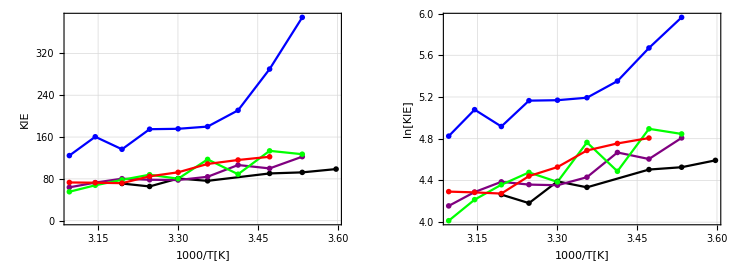

```mathematica
GraphicsRow[{
ListLinePlot[{KIEWTR,KIEi553vR,KIEi553lR,KIEi553aR,KIEi553gR},
Axes->False,Frame->True,FrameLabel->{"1000/T[K]","KIE"},
PlotRange->All,PlotStyle->{Black,Purple,Green,Red,Blue},AspectRatio->0.75,PlotTheme->{"Detailed","PlotMarkers","LargeLabels"}],
ListLinePlot[{lnKIEWTR,lnKIEi553vR,lnKIEi553lR,lnKIEi553aR,lnKIEi553gR},
Axes->False,Frame->True,FrameLabel->{"1000/T[K]","ln[KIE]"},
PlotRange->All,PlotStyle->{Black,Purple,Green,Red,Blue},AspectRatio->0.75,PlotTheme->{"Detailed","PlotMarkers","LargeLabels"}]
}]
```

## Fits for SLO WT

```mathematica
Δ=-5.4;
λ=13.4;
```

```mathematica
f6KIEWT[M_,R_,Ω_]:=Sqrt[Sum[(KIE6[KIEWT⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEWT⟦i,2⟧)^2,{i,1,Length[KIEWT]}]];
```

```mathematica
f7KIEWT[M_,R_,Ω_]:=Sqrt[Sum[(KIE7[KIEWT⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEWT⟦i,2⟧)^2,{i,1,Length[KIEWT]}]];
```

```mathematica
fKIEWT[M_,R_,Ω_]:=Sqrt[Sum[(KIE[KIEWT⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEWT⟦i,2⟧)^2,{i,1,Length[KIEWT]}]];
```

```mathematica
fgKIEWT[M_,R_,Ω_]:=Sqrt[Sum[(KIEg[KIEWT⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEWT⟦i,2⟧)^2,{i,1,Length[KIEWT]}]];
```

```mathematica
fKIEWTF[M_,R_,Ω_]:=Module[{rmsd,KIEth,KIEexp,T,npoints,RR},
RR=R0[R];
npoints=Length[KIEWT];
rmsd=0;
Do[
T=KIEWT⟦i,1⟧;
KIEth=KIE[T,Δ,λ,RR,M,Ω,2,2];
KIEexp=KIEWT⟦i,2⟧;
rmsd+=(KIEexp-KIEth)^2,
{i,1,npoints}];
Sqrt[rmsd]/npoints
];
```

```mathematica
fgKIEWTF[M_,R_,Ω_]:=Module[{rmsd,KIEth,KIEexp,T,npoints,RR},
RR=R0[R];
npoints=Length[KIEWT];
rmsd=0;
Do[
T=KIEWT⟦i,1⟧;
KIEth=KIEg[T,Δ,λ,RR,M,Ω,2,2];
KIEexp=KIEWT⟦i,2⟧;
rmsd+=(KIEexp-KIEth)^2,
{i,1,npoints}];
Sqrt[rmsd]/npoints
];
```

For Mass = 100 amu

```mathematica
FindMinimum[{fgKIEWT[100,2.7,W],W>50},{W,200}]
```

{12.0938,{W→173.9}}

```mathematica
KIEgWTmin[M_,R_]:=FindMinimum[{fgKIEWT[M,R,W],50<W<1000},{W,200}]⟦1⟧;
```

```mathematica
KIEg[303.0,Δ,λ,R0[2.7],100.0,173.9,2,2]
```

77.6461

```mathematica
Table[RateHg[303.0,Δ,λ,R0[2.7],100.0,173.9,i,j],{i,0,2},{j,0,2}]//TableForm
```

5.22125×10^7 | 916869. | 119.527
9.48855×10^9 | 7.22811×10^9 | 3.02738×10^7
2.83963×10^10 | 7.10742×10^11 | 7.34479×10^10

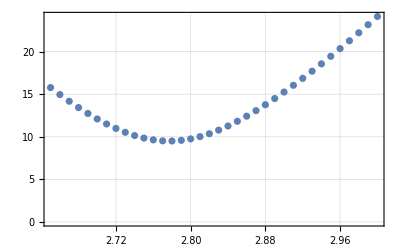

```mathematica
ListPlot[Table[{Ri,KIEgWTmin[100,Ri]},{Ri,2.65,3.0,0.01}],PlotTheme->"Detailed"]
```

```mathematica
KIEgWTmin[100,2.77]
```

9.52358

```mathematica
FindMinimum[{fgKIEWT[100,2.77,W],W>50},{W,200}]
```

{9.52358,{W→132.832}}

For Mass = 10 amu

```mathematica
FindMinimum[{fgKIEWT[10,2.78,W],W>50},{W,400}]
```

{13.1222,{W→479.554}}

```mathematica
KIEg[303.0,Δ,λ,R0[2.78],10.0,479.554,2,2]
```

78.0803

```mathematica
Table[RateHg[303.0,Δ,λ,R0[2.7],10.0,479.554,i,j],{i,0,2},{j,0,2}]//TableForm
```

1.43393×10^8 | 1.94765×10^6 | 202.403
2.00629×10^10 | 1.18508×10^10 | 3.99322×10^7
4.7517×10^10 | 9.28945×10^11 | 7.90538×10^10

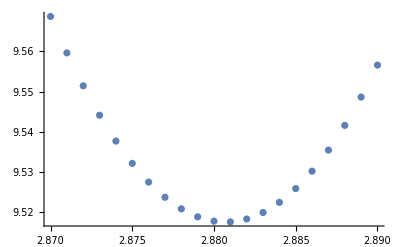

```mathematica
ListPlot[Table[{Ri,KIEgWTmin[10,Ri]},{Ri,2.87,2.89,0.001}]]
```

```mathematica
KIEgWTmin[10,2.881]
```

9.51764

```mathematica
FindMinimum[{fgKIEWT[10,2.881,W],W>50},{W,400}]
```

{9.51764,{W→368.156}}

```mathematica
WTg100={2.77,132.832};
WTg10={2.881,368.156};
```

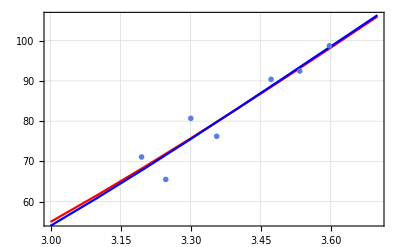

```mathematica
Show[
{ListLinePlot[Table[{x,KIEg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Red,PlotTheme->"Detailed"],
ListLinePlot[Table[{x,KIEg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Blue,PlotTheme->"Detailed"],
ListPlot[KIEWTR,PlotTheme->"Business"]}
]
```

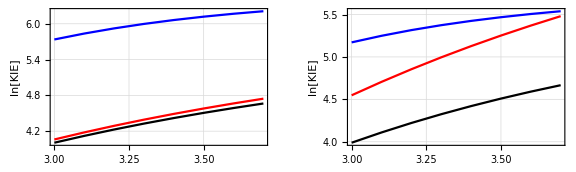

```mathematica
GraphicsRow[{
ListLinePlot[
{Table[{x,Log@Re@KIEg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@Re@KIElowTg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@Re@KIE7g[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}]},
PlotStyle->{Black,Blue,Red},Axes->False,Frame->True,PlotTheme->"Detailed",
FrameLabel->{"1000/T[K]","ln[KIE]","M = 100"}
],
ListLinePlot[
{Table[{x,Log@Re@KIEg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@Re@KIElowTg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@Re@KIE7g[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}]},
PlotStyle->{Black,Blue,Red},Axes->False,Frame->True,PlotTheme->"Detailed",
FrameLabel->{"1000/T[K]","ln[KIE]","M = 10"}
]
},ImageSize->Large,AspectRatio->0.75]
```

Refit V^el to match the absolute rate at 303K

```mathematica
TotalrateHg[303,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]
```

1.27526×10^7

```mathematica
V Sqrt[297.11/%]au2kcal
```

0.00482681

```mathematica
V=SetAccuracy[% kcal2au,AccN]
```

7.6920060939593759628644942250019767016055994×10^-6

```mathematica
% au2cm
```

1.6882

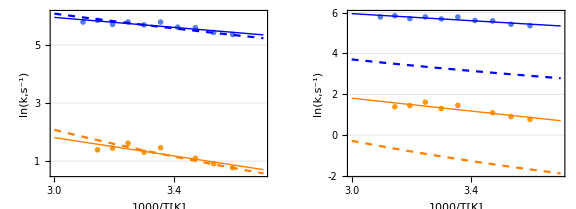

```mathematica
AH=8.54005;
AD=6.54083;
λH=15.8079;
λD=22.0148;
GraphicsRow[{
Show[{
ListPlot[{ratesHWTR,ratesDWTR},PlotTheme->"Business"],
Plot[AH -(Δ+λH)^2/(4 λH 1000 kb au2kcal)x,{x,3.0,3.7},PlotStyle->{Blue,Thin}],
Plot[AD -(Δ+λD)^2/(4 λD 1000 kb au2kcal)x,{x,3.0,3.7},PlotStyle->{Orange,Thin}],
ListLinePlot[Table[{x,Log@TotalrateHg[1000.0/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->{Blue,Dashed}],
ListLinePlot[Table[{x,Log@TotalrateDg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->{Orange,Dashed}]
},
Axes->False,Frame->True,FrameLabel->{"1000/T[K]","ln(k,s^-1)","M = 100 amu"},PlotRange->All,AspectRatio->0.75,PlotTheme->"Detailed"],
Show[{
ListPlot[{ratesHWTR,ratesDWTR},PlotTheme->"Business"],
Plot[AH -(Δ+λH)^2/(4 λH 1000 kb au2kcal)x,{x,3.0,3.7},PlotStyle->{Blue,Thin}],
Plot[AD -(Δ+λD)^2/(4 λD 1000 kb au2kcal)x,{x,3.0,3.7},PlotStyle->{Orange,Thin}],
ListLinePlot[Table[{x,Log@TotalrateHg[1000.0/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->{Blue,Dashed}],
ListLinePlot[Table[{x,Log@TotalrateDg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->{Orange,Dashed}]
},
Axes->False,Frame->True,FrameLabel->{"1000/T[K]","ln(k,s^-1)","M = 10 amu"},PlotRange->All,AspectRatio->0.75,PlotTheme->"Detailed"]
},ImageSize->Large]
```

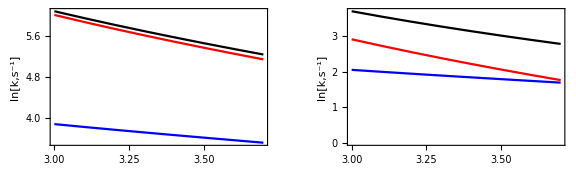

```mathematica
GraphicsRow[{
ListLinePlot[
{Table[{x,Log@TotalrateHg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@TotalratelowHg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@TotalrateH7g[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}]},
PlotStyle->{Black,Blue,Red},Axes->False,Frame->True,
FrameLabel->{"1000/T[K]","ln[k,s^-1]","M = 100"}
],
ListLinePlot[
{Table[{x,Log@TotalrateHg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@TotalratelowHg[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}],
Table[{x,Log@TotalrateH7g[1000/x,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]},{x,3.0,3.7,0.1}]},
PlotStyle->{Black,Blue,Red},Axes->False,Frame->True,
FrameLabel->{"1000/T[K]","ln[k,s^-1]","M = 10"}
]
},ImageSize->Large]
```

## Rate and KIE temperature dependences

### Fit for WT with mass 100 amu (set WTg100)

```mathematica
Ω=WTg100⟦2⟧;
MM=100;
RR=WTg100⟦1⟧;
μmax=2;
νmax=2;
mmax=15;
nmax=15;
```

#### Rates

```mathematica
lgrateHtableT100=Table[{1000./T,Log10[TotalrateH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270.,340.,10.}];
lgrateHgtableT100=Table[{1000./T,Log10[TotalrateHg[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270.,340.,10.}];
lgUKrateHtableT100=Table[{1000./T,Log10[TotalrateUKH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270.,340.,10.}];
```

```mathematica
lgDAQrateHtableT100=ParallelTable[{1000./T,Log10[totalRateDAQH[T,Δ,λ,R0[RR],MM,Ω,μmax,mmax,νmax,nmax]]},{T,{270,300,340}}];
```

```mathematica
lgrateq10HtableT100=ParallelTable[{1000./T,Log10[Totalrateq10fluxH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,{270,300,340}}];
```

```mathematica
lnrateHtableT100=MapAt[#/Log10[ⅇ]&,lgrateHtableT100,{All,2}];
lnrateHgtableT100=MapAt[#/Log10[ⅇ]&,lgrateHgtableT100,{All,2}];
lnUKrateHtableT100=MapAt[#/Log10[ⅇ]&,lgUKrateHtableT100,{All,2}];
lnDAQrateHtableT100=MapAt[#/Log10[ⅇ]&,lgDAQrateHtableT100,{All,2}];
lnrateq10HtableT100=MapAt[#/Log10[ⅇ]&,lgrateq10HtableT100,{All,2}];
```

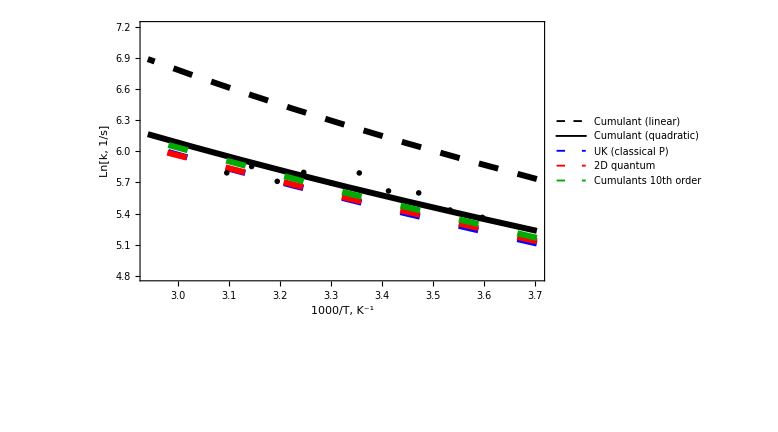

```mathematica
kvsTM100=Show[
ListLinePlot[{lnrateHtableT100,lnrateHgtableT100,lnUKrateHtableT100,lnDAQrateHtableT100,lnrateq10HtableT100},
Axes->False,Frame->True,PlotRange->{4.8,7.2},
FrameLabel->{"1000/T, K^-1","Ln[k, 1/s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
PlotLegends->{
"Cumulant (linear)",
"Cumulant (quadratic)",
"UK (classical P)",
"2D quantum",
"Cumulants 10th order"
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
Epilog->Inset[Style["(a)",Black,"Helvetica",28],{3.65,3.}]
],
ListPlot[{ratesHWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

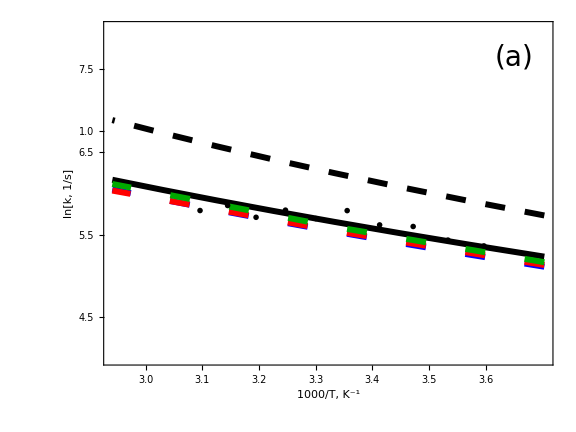

```mathematica
kvsTM100top=Show[
ListLinePlot[{lnrateHtableT100,lnrateHgtableT100,lnUKrateHtableT100,lnDAQrateHtableT100,lnrateq10HtableT100},
Axes->False,Frame->True,PlotRange->{4.0,8},
FrameLabel->{Style["1000/T, K^-1",Transparent],"ln[k, 1/s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
LabelStyle->Black,
FrameTicksStyle->{{Black,Black},{Transparent,Black}},
FrameTicks->{
{{{4.5,"4.5",{0.02,0}},{5.5,"5.5",{0.02,0}},{6.5,"6.5",{0.02,0}},{6.75,Style["1.0",Transparent],{0.02,0}},{7.5,"7.5",{0.02,0}}},None},
{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(a)",Black,"Helvetica",28],{3.65,7.65}]
],
ListPlot[{ratesHWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

#### KIE

```mathematica
mmax=15;
nmax=15;
```

```mathematica
lgKIEtableT100=ParallelTable[{1000/T,Log10[KIE[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgKIEgtableT100=ParallelTable[{1000/T,Log10[KIEg[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgUKKIEtableT100=ParallelTable[{1000/T,Log10[KIEUK[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
```

```mathematica
lgDAQKIEtableT100=ParallelTable[{1000/T,Log10[KIEDAQ[T,Δ,λ,R0[RR],MM,Ω,μmax,mmax,νmax,nmax]]},{T,{270,300,340}}];
```

```mathematica
lgKIEq10tableT100=ParallelTable[{1000/T,Log10[KIEq10flux[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,{270,300,340}}];
```

```mathematica
lnKIEtableT100=MapAt[#/Log10[ⅇ]&,lgKIEtableT100,{All,2}];
lnKIEgtableT100=MapAt[#/Log10[ⅇ]&,lgKIEgtableT100,{All,2}];
lnUKKIEtableT100=MapAt[#/Log10[ⅇ]&,lgUKKIEtableT100,{All,2}];
lnDAQKIEtableT100=MapAt[#/Log10[ⅇ]&,lgDAQKIEtableT100,{All,2}];
lnKIEq10tableT100=MapAt[#/Log10[ⅇ]&,lgKIEq10tableT100,{All,2}];
```

```mathematica
KIEtableT100=MapAt[10^#&,lgKIEtableT100,{All,2}];
KIEgtableT100=MapAt[10^#&,lgKIEgtableT100,{All,2}];
UKKIEtableT100=MapAt[10^#&,lgUKKIEtableT100,{All,2}];
DAQKIEtableT100=MapAt[10^#&,lgDAQKIEtableT100,{All,2}];
KIEq10tableT100=MapAt[10^#&,lgKIEq10tableT100,{All,2}];
```

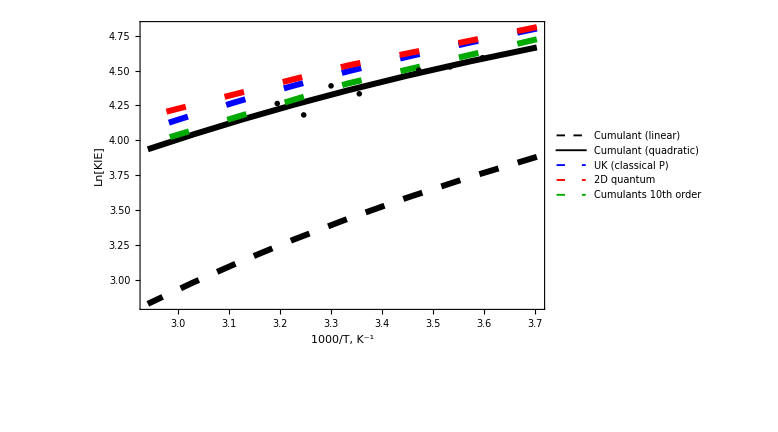

```mathematica
KIEvsTM100=Show[
ListLinePlot[{lnKIEtableT100,lnKIEgtableT100,lnUKKIEtableT100,lnDAQKIEtableT100,lnKIEq10tableT100},
Axes->False,Frame->True,PlotRange->All,
FrameLabel->{"1000/T, K^-1","Ln[KIE]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
PlotLegends->{
"Cumulant (linear)",
"Cumulant (quadratic)",
"UK (classical P)",
"2D quantum",
"Cumulants 10th order"
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
Epilog->Inset[Style["(b)",Black,"Helvetica",28],{3.65,2.2}]
],
ListPlot[{lnKIEWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

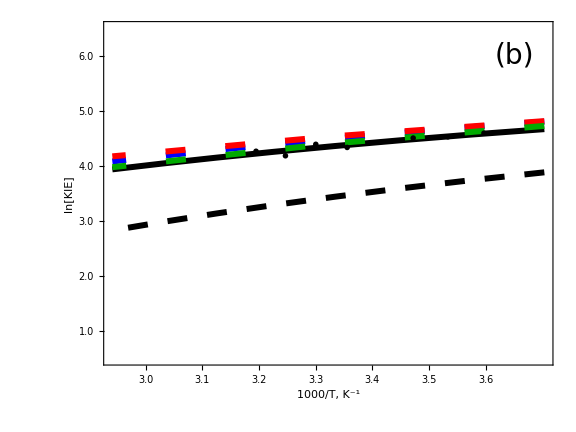

```mathematica
KIEvsTM100bottom=Show[
ListLinePlot[{lnKIEtableT100,lnKIEgtableT100,lnUKKIEtableT100,lnDAQKIEtableT100,lnKIEq10tableT100},
Axes->False,Frame->True,PlotRange->{0.5,6.5},
FrameLabel->{"1000/T, K^-1","ln[KIE]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
FrameTicks->{{{{1.0,"1.0",{0.02,0}},{2.0,"2.0",{0.02,0}},{3.0,"3.0",{0.02,0}},{4.0,"4.0",{0.02,0}},{5.0,"5.0",{0.02,0}},{6.0,"6.0",{0.02,0}}},None},{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(b)",Black,"Helvetica",28],{3.65,6}]
],
ListPlot[{lnKIEWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

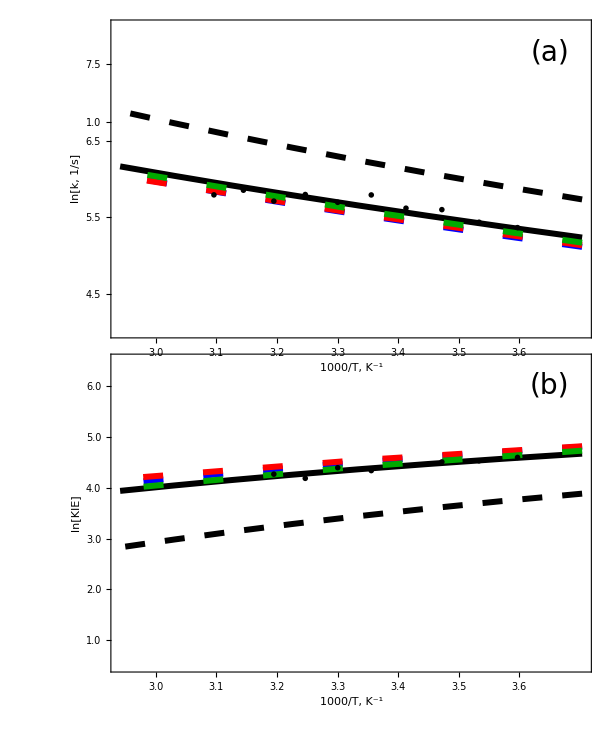

```mathematica
GraphicsColumn[{kvsTM100top,KIEvsTM100bottom},Spacings->-71]
```

### Fit for WT with mass 10 amu (set WTg10)

```mathematica
WTg10
```

{2.881,368.156}

```mathematica
{Δ,λ}
```

{-5.4,13.4}

```mathematica
Ω=WTg10⟦2⟧;
MM=10;
RR=WTg10⟦1⟧;
μmax=2;
νmax=2;
mmax=15;
nmax=15;
```

Refit V^el to match the absolute rate at 303K

```mathematica
TotalrateHg[303,Δ,λ,R0[WTg10⟦1⟧],10,WTg10⟦2⟧,2,2]
```

26.512

```mathematica
V Sqrt[297.11/%]au2kcal
```

0.0161584

```mathematica
V=SetAccuracy[% kcal2au,AccN]
```

0.0000257499730594749827753894844128979002562118694

```mathematica
% au2cm
```

5.65145

```mathematica
V au2cm
```

5.65145

#### Rates

```mathematica
lgrateHtableT10=ParallelTable[{1000/T,Log10[TotalrateH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgrateHgtableT10=ParallelTable[{1000/T,Log10[TotalrateHg[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgUKrateHtableT10=ParallelTable[{1000/T,Log10[TotalrateUKqH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
```

```mathematica
lgDAQrateHtableT10=ParallelTable[{1000/T,Log10[totalRateDAQH[T,Δ,λ,R0[RR],MM,Ω,μmax,mmax,νmax,nmax]]},{T,{270,300,340}}];
```

```mathematica
lgrateq10HtableT10=ParallelTable[{1000/T,Log10[Totalrateq10fluxH[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,{270,300,340}}];
```

```mathematica
lnrateHtableT10=MapAt[#/Log10[ⅇ]&,lgrateHtableT10,{All,2}];
lnrateHgtableT10=MapAt[#/Log10[ⅇ]&,lgrateHgtableT10,{All,2}];
lnUKrateHtableT10=MapAt[#/Log10[ⅇ]&,lgUKrateHtableT10,{All,2}];
lnDAQrateHtableT10=MapAt[#/Log10[ⅇ]&,lgDAQrateHtableT10,{All,2}];
lnrateq10HtableT10=MapAt[#/Log10[ⅇ]&,lgrateq10HtableT10,{All,2}];
```

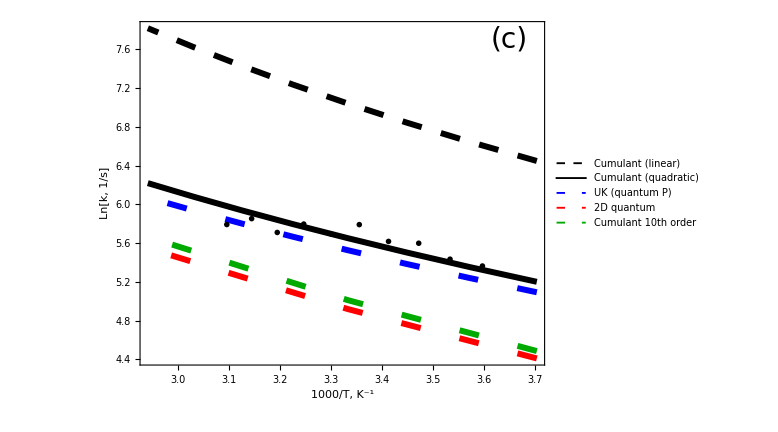

```mathematica
kvsTM10=Show[
ListLinePlot[{lnrateHtableT10,lnrateHgtableT10,lnUKrateHtableT10,lnDAQrateHtableT10,lnrateq10HtableT10},
Axes->False,Frame->True,PlotRange->All,
FrameLabel->{"1000/T, K^-1","ln[k, 1/s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
PlotLegends->{
"Cumulant (linear)",
"Cumulant (quadratic)",
"UK (quantum P)",
"2D quantum",
"Cumulant 10th order"
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
Epilog->Inset[Style["(c)",Black,"Helvetica",28],{3.65,7.7}]
],
ListPlot[{ratesHWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

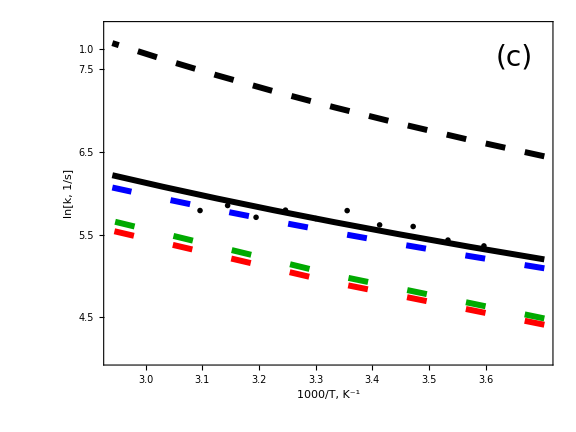

```mathematica
kvsTM10top=Show[
ListLinePlot[{lnrateHtableT10,lnrateHgtableT10,lnUKrateHtableT10,lnDAQrateHtableT10,lnrateq10HtableT10},
Axes->False,Frame->True,PlotRange->{4.0,8},
FrameLabel->{Style["1000/T, K^-1",Transparent],"ln[k, 1/s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
LabelStyle->Black,
FrameTicksStyle->{{Black,Black},{Transparent,Black}},
FrameTicks->{
{{{4.5,"4.5",{0.02,0}},{5.5,"5.5",{0.02,0}},{6.5,"6.5",{0.02,0}},{7.5,"7.5",{0.02,0}},{7.75,Style["1.0",Transparent],{0,0}}},None},
{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(c)",Black,"Helvetica",28],{3.65,7.65}]
],
ListPlot[{ratesHWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

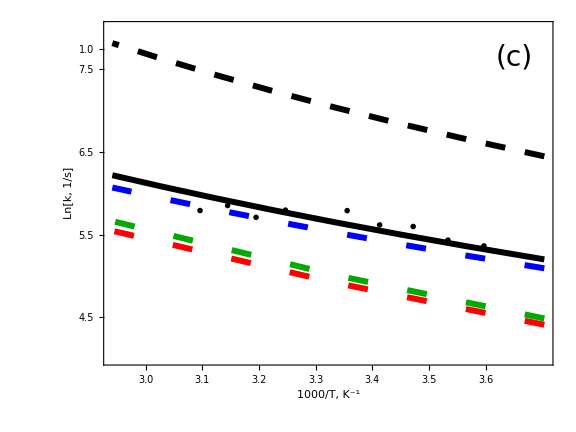

```mathematica
kvsTM10topc=Show[
ListLinePlot[{lnrateHtableT10,lnrateHgtableT10,lnUKrateHtableT10,lnDAQrateHtableT10,lnrateq10HtableT10},
Axes->False,Frame->True,PlotRange->{4.0,8},
FrameLabel->{Style["1000/T, K^-1",Transparent],Style["Ln[k, 1/s]",Transparent]},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
LabelStyle->Black,
FrameTicksStyle->{{Transparent,Black},{Transparent,Black}},
FrameTicks->{
{{{4.5,"4.5",{0.02,0}},{5.5,"5.5",{0.02,0}},{6.5,"6.5",{0.02,0}},{7.5,"7.5",{0.02,0}},{7.75,Style["1.0",Transparent],{0,0}}},None},
{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(c)",Black,"Helvetica",28],{3.65,7.65}]
],
ListPlot[{ratesHWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

#### KIE

```mathematica
mmax=20;
nmax=20;
```

```mathematica
lgKIEtableT10=ParallelTable[{1000/T,Log10[KIE[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgKIEgtableT10=ParallelTable[{1000/T,Log10[KIEg[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
lgUKKIEtableT10=ParallelTable[{1000/T,Log10[KIEUKq[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,270,340,10}];
```

```mathematica
lgDAQKIEtableT10=ParallelTable[{1000/T,Log10[KIEDAQ[T,Δ,λ,R0[RR],MM,Ω,μmax,mmax,νmax,nmax]]},{T,{270,300,340}}];
```

```mathematica
lgKIEq10tableT10=ParallelTable[{1000/T,Log10[KIEq10flux[T,Δ,λ,R0[RR],MM,Ω,μmax,νmax]]},{T,{270,300,340}}];
```

```mathematica
lnKIEtableT10=MapAt[#/Log10[ⅇ]&,lgKIEtableT10,{All,2}];
lnKIEgtableT10=MapAt[#/Log10[ⅇ]&,lgKIEgtableT10,{All,2}];
lnUKKIEtableT10=MapAt[#/Log10[ⅇ]&,lgUKKIEtableT10,{All,2}];
lnDAQKIEtableT10=MapAt[#/Log10[ⅇ]&,lgDAQKIEtableT10,{All,2}];
lnKIEq10tableT10=MapAt[#/Log10[ⅇ]&,lgKIEq10tableT10,{All,2}];
```

```mathematica
KIEtableT10=MapAt[10^#&,lgKIEtableT10,{All,2}];
KIEgtableT10=MapAt[10^#&,lgKIEgtableT10,{All,2}];
UKKIEtableT10=MapAt[10^#&,lgUKKIEtableT10,{All,2}];
DAQKIEtableT10=MapAt[10^#&,lgDAQKIEtableT10,{All,2}];
KIEq10tableT10=MapAt[10^#&,lgKIEq10tableT10,{All,2}];
```

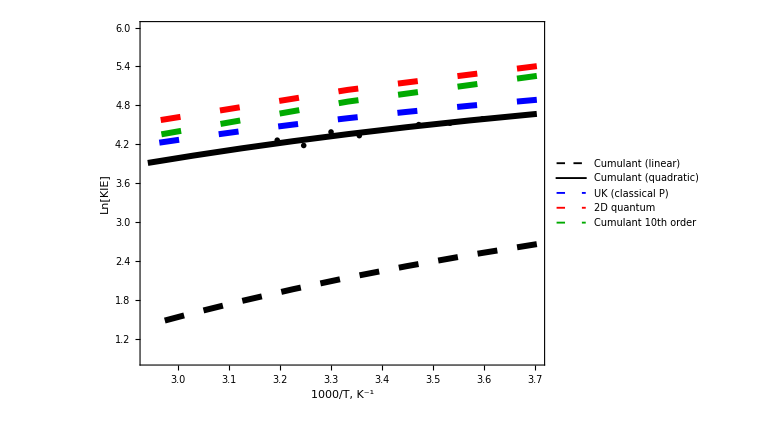

```mathematica
KIEvsTM10=Show[
ListLinePlot[{lnKIEtableT10,lnKIEgtableT10,lnUKKIEtableT10,lnDAQKIEtableT10,lnKIEq10tableT10},
Axes->False,Frame->True,PlotRange->{0.9,5.99},
FrameLabel->{"1000/T, K^-1","Ln[KIE]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
PlotLegends->{
"Cumulant (linear)",
"Cumulant (quadratic)",
"UK (classical P)",
"2D quantum",
"Cumulant 10th order"
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
Epilog->Inset[Style["(d)",Black,"Helvetica",28],{3.65,150}]
],
ListPlot[{lnKIEWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

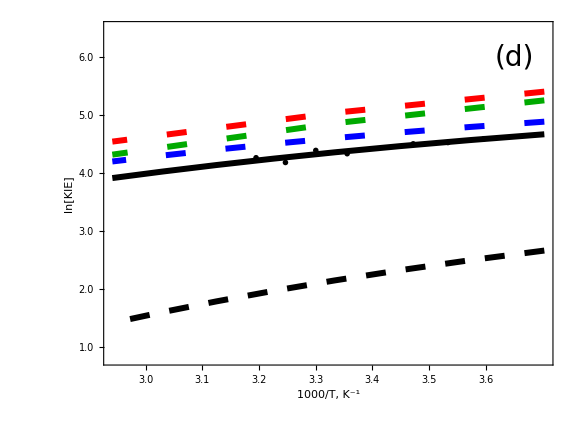

```mathematica
KIEvsTM10bottom=Show[
ListLinePlot[{lnKIEtableT10,lnKIEgtableT10,lnUKKIEtableT10,lnDAQKIEtableT10,lnKIEq10tableT10},
Axes->False,Frame->True,PlotRange->{0.8,6.5},
FrameLabel->{"1000/T, K^-1","ln[KIE]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
FrameTicks->{{{{1,"1.0",{0.02,0}},{2,"2.0",{0.02,0}},{3,"3.0",{0.02,0}},{4,"4.0",{0.02,0}},{5,"5.0",{0.02,0}},{6,"6.0",{0.02,0}}},None},{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(d)",Black,"Helvetica",28],{3.65,6}]
],
ListPlot[{lnKIEWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

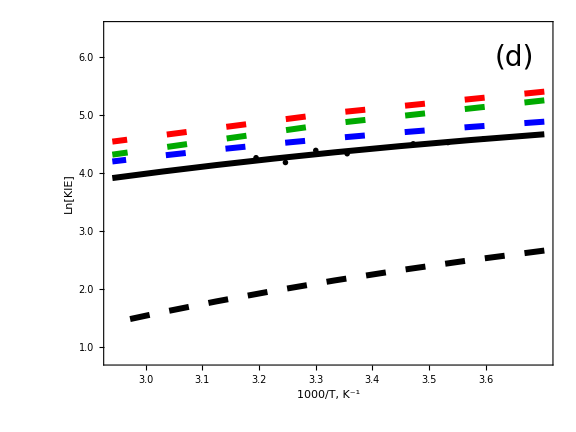

```mathematica
KIEvsTM10bottomd=Show[
ListLinePlot[{lnKIEtableT10,lnKIEgtableT10,lnUKKIEtableT10,lnDAQKIEtableT10,lnKIEq10tableT10},
Axes->False,Frame->True,PlotRange->{0.8,6.5},
FrameLabel->{"1000/T, K^-1",Style["Ln[KIE]",Transparent]},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Dashing[0.025],Thickness[0.0075]},
{Black, Thickness[0.0075]},
{Blue, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Red, Dashing[{0.025,0.05}],Thickness[0.0075]},
{Darker@Green, Dashing[{0.025,0.05}],Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->{{Transparent,Black},{Black,Black}},
LabelStyle->Black,
FrameTicks->{{{{1,"1.0",{0.02,0}},{2,"2.0",{0.02,0}},{3,"3.0",{0.02,0}},{4,"4.0",{0.02,0}},{5,"5.0",{0.02,0}},{6,"6.0",{0.02,0}}},None},{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}}},None}},
Epilog->Inset[Style["(d)",Black,"Helvetica",28],{3.65,6}]
],
ListPlot[{lnKIEWTR},PlotTheme->"OpenMarkersThick",PlotStyle->Black]
]
```

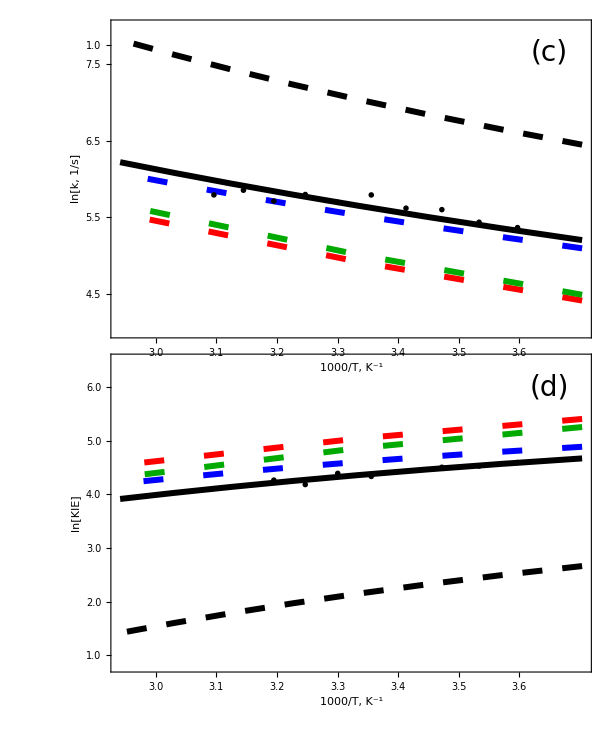

```mathematica
GraphicsColumn[{kvsTM10top,KIEvsTM10bottom},Spacings->-71]
```

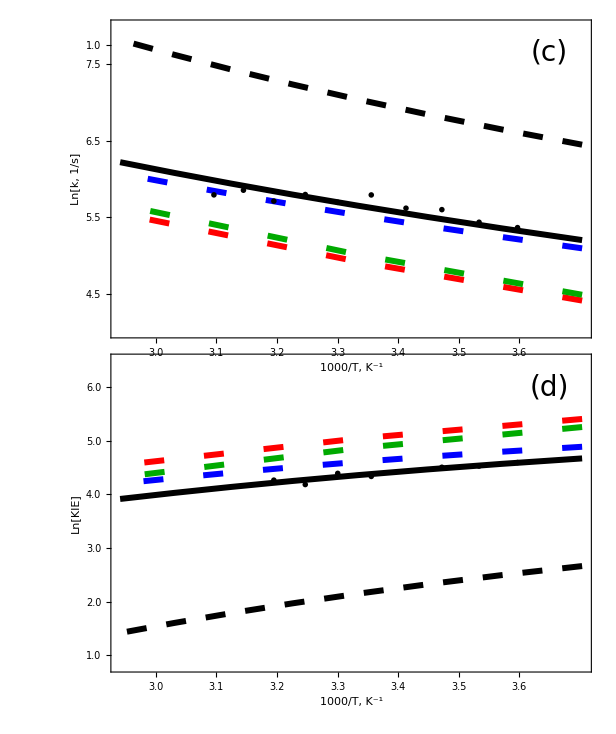

```mathematica
GraphicsColumn[{kvsTM10topc,KIEvsTM10bottomd},Spacings->-71]
```

### Combined 4-panel figure for WT with masses 10 amu and 100 amu (sets WTg100 and WTg10)

```mathematica
Figure3abcd=GraphicsRow[{
GraphicsColumn[{kvsTM100top,KIEvsTM100bottom},Spacings->-68],
GraphicsColumn[{kvsTM10top,KIEvsTM10bottom},Spacings->-68]
},Spacings->{-40,0}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Faraday-2016-KIE

```mathematica
Export["Figure3abcd.tif",Figure3abcd,ImageResolution->600]
```

Figure3abcd.tif

```mathematica
Export["Figure3abcd.eps",Figure3abcd,ImageResolution->600]
```

Figure3abcd.eps

```mathematica
Export["Figure3abcd.pdf",Figure3abcd,ImageResolution->600]
```

Figure3abcd.pdf

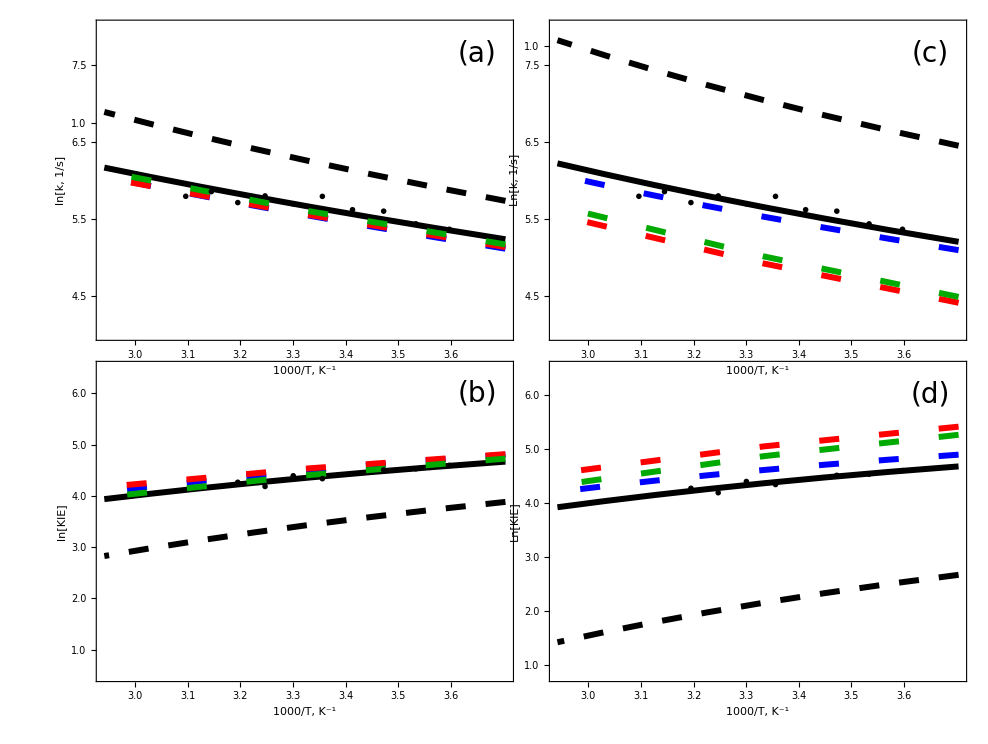

```mathematica
Figure3abcd4=GraphicsGrid[{
{kvsTM100top,kvsTM10topc},
{KIEvsTM100bottom,KIEvsTM10bottomd}
},
Spacings->{-88,-66}]
```

```mathematica
Export["Figure3abcd4.tif",Figure3abcd4,ImageResolution->600]
```

Figure3abcd4.tif

```mathematica
Export["Figure3abcd4.eps",Figure3abcd4,ImageResolution->600]
```

Figure3abcd4.eps

```mathematica
Export["Figure3abcd4.pdf",Figure3abcd4,ImageResolution->600]
```

Figure3abcd4.pdf

## Fits for i553 mutants

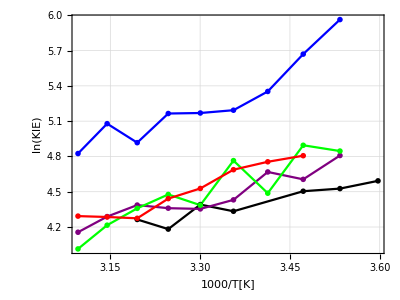

```mathematica
ListLinePlot[{lnKIEWTR,lnKIEi553vR,lnKIEi553lR,lnKIEi553aR,lnKIEi553gR},
Axes->False,Frame->True,FrameLabel->{"1000/T[K]","ln(KIE)"},
PlotRange->All,PlotStyle->{Black,Purple,Green,Red,Blue},AspectRatio->0.75,PlotTheme->{"Detailed","PlotMarkers","LargeLabels"}]
```

```mathematica
fgKIEi553v[M_,R_,Ω_]:=Sqrt[Sum[(KIEg[KIEi553v⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEi553v⟦i,2⟧)^2,{i,1,Length[KIEi553v]}]];
fgKIEi553a[M_,R_,Ω_]:=Sqrt[Sum[(KIEg[KIEi553a⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEi553a⟦i,2⟧)^2,{i,1,Length[KIEi553a]}]];
fgKIEi553l[M_,R_,Ω_]:=Sqrt[Sum[(KIEg[KIEi553l⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEi553l⟦i,2⟧)^2,{i,1,Length[KIEi553l]}]];
fgKIEi553g[M_,R_,Ω_]:=Sqrt[Sum[(KIEg[KIEi553g⟦i,1⟧,Δ,λ,R0[R],M,Ω,2,2]-KIEi553g⟦i,2⟧)^2,{i,1,Length[KIEi553g]}]];
```

```mathematica
fgKIEi553vWmin[M_,R_]:=FindMinimum[{fgKIEi553v[M,R,W],50<W<1000},{W,200}]⟦1⟧;
fgKIEi553lWmin[M_,R_]:=FindMinimum[{fgKIEi553l[M,R,W],50<W<1000},{W,200}]⟦1⟧;
fgKIEi553aWmin[M_,R_]:=FindMinimum[{fgKIEi553a[M,R,W],50<W<1000},{W,200}]⟦1⟧;
fgKIEi553gWmin[M_,R_]:=FindMinimum[{fgKIEi553g[M,R,W],50<W<1000},{W,200}]⟦1⟧;
```

### Manual fits for M = 10 and 100 amu

#### i553v

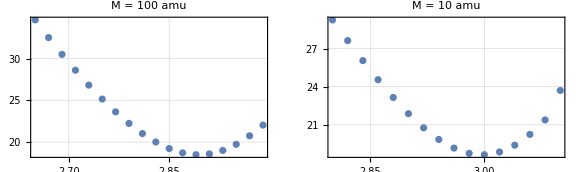

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553vWmin[100,Ri]},{Ri,2.65,3.0,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553vWmin[10,Ri]},{Ri,2.8,3.1,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553v[100,2.895,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553v[10,2.99,W],50<W<1000},{W,300}]
```

{18.4797,{W→105.298}}

{18.6628,{W→319.044}}

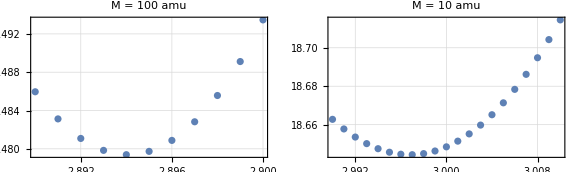

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553vWmin[100,Ri]},{Ri,2.89,2.90,0.001}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553vWmin[10,Ri]},{Ri,2.99,3.01,0.001}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553v[100,2.894,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553v[10,2.997,W],50<W<1000},{W,300}]
```

{18.4794,{W→105.462}}

{18.6444,{W→316.332}}

```mathematica
i553v100g={2.894,105.462};
i553v10g={2.997,316.332};
```

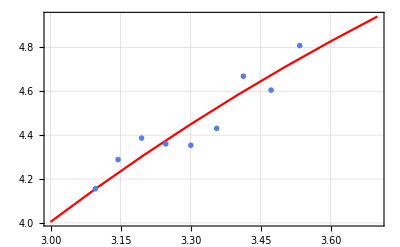

```mathematica
Show[
{ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553v100g⟦1⟧],100,i553v100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Red,PlotTheme->"Detailed"],
ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553v100g⟦1⟧],10,i553v10g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Blue,PlotTheme->"Detailed"],
ListPlot[lnKIEi553vR,PlotTheme->"Business"]}
]
```

#### i553l

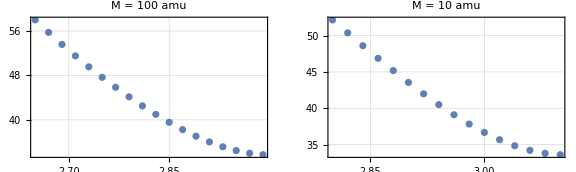

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553lWmin[100,Ri]},{Ri,2.65,3.0,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553lWmin[10,Ri]},{Ri,2.8,3.1,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553l[100,3.0,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553l[10,3.1,W],50<W<1000},{W,300}]
```

{33.6785,{W→93.0049}}

{33.6148,{W→292.42}}

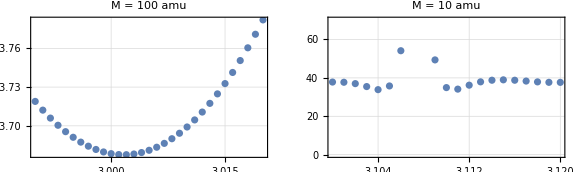

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553lWmin[100,Ri]},{Ri,2.99,3.02,0.001}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,FindMinimum[{fgKIEi553l[100,Ri,W],50<W<1000},{W,300}]⟦1⟧},{Ri,3.10,3.12,0.001}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553l[100,3.002,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553l[10,3.104,W],50<W<1000},{W,300}]
```

{33.6777,{W→92.8099}}

{34.7858,{W→266.419}}

```mathematica
i553l100g={3.002,92.8099};
i553l10g={3.104,266.419};
```

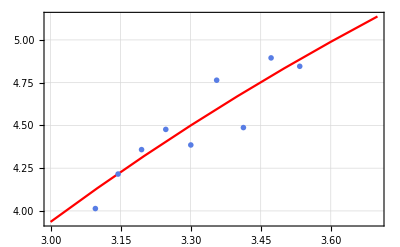

```mathematica
Show[
{ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553l100g⟦1⟧],100,i553l100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Red,PlotTheme->"Detailed"],
ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553l100g⟦1⟧],10,i553l10g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Blue,PlotTheme->"Detailed"],
ListPlot[lnKIEi553lR,PlotTheme->"Business"]}
]
```

#### i553a

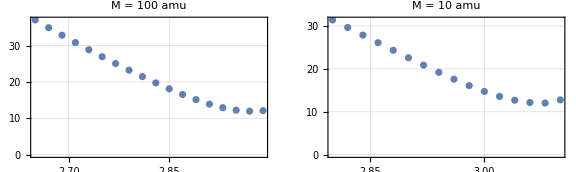

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553aWmin[100,Ri]},{Ri,2.65,3.0,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553aWmin[10,Ri]},{Ri,2.8,3.1,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553a[100,2.97,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553a[10,3.07,W],50<W<1000},{W,300}]
```

{11.9588,{W→96.6774}}

{12.046,{W→296.509}}

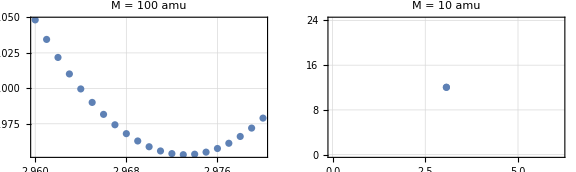

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553aWmin[100,Ri]},{Ri,2.96,2.98,0.001}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553aWmin[10,Ri]},{Ri,3.07,3.08,0.002}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
Table[{Ri,fgKIEi553aWmin[10,Ri]},{Ri,3.07,3.08,0.001}]//TableForm
```

3.07 | 12.046
3.071 | 12.0408
3.072 | 12.0367
3.073 | 12.0337
3.074 | 12.0318
3.075 | 12.031
3.076 | 12.0314
3.077 | 12.033
3.078 | 12.0358
3.079 | 12.0396
3.08 | 12.0445

```mathematica
FindMinimum[{fgKIEi553a[100,2.973,W],50<W<1000},{W,100}]
FindMinimum[{fgKIEi553a[10,3.075,W],50<W<1000},{W,300}]
```

{11.9532,{W→96.3405}}

{12.031,{W→295.112}}

```mathematica
i553a100g={2.973,96.3405};
i553a10g={3.075,295.112};
```

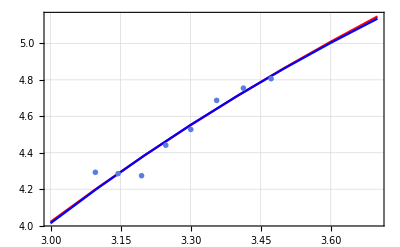

```mathematica
Show[
{ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553a100g⟦1⟧],100,i553a100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Red,PlotTheme->"Detailed"],
ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553a10g⟦1⟧],10,i553a10g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Blue,PlotTheme->"Detailed"],
ListPlot[lnKIEi553aR,PlotTheme->"Business"]}
]
```

#### i553g

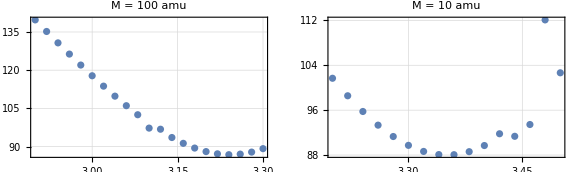

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553gWmin[100,Ri]},{Ri,2.9,3.3,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553gWmin[10,Ri]},{Ri,3.2,3.5,0.02}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553g[100,3.22,W],50<W<1000},{W,200}]
FindMinimum[{fgKIEi553g[10,3.35,W],50<W<1000},{W,300}]
```

{87.1476,{W→83.1725}}

{88.0066,{W→257.681}}

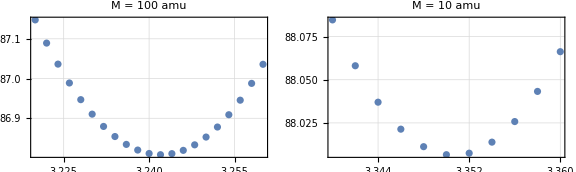

```mathematica
GraphicsRow[{
ListPlot[Table[{Ri,fgKIEi553gWmin[100,Ri]},{Ri,3.22,3.26,0.002}],PlotTheme->{"Detailed"},PlotLabel->"M = 100 amu"],
ListPlot[Table[{Ri,fgKIEi553gWmin[10,Ri]},{Ri,3.34,3.36,0.002}],PlotTheme->{"Detailed"},PlotLabel->"M = 10 amu"]
},ImageSize->Large]
```

```mathematica
FindMinimum[{fgKIEi553g[100,3.242,W],50<W<1000},{W,100}]
FindMinimum[{fgKIEi553g[10,3.351,W],50<W<1000},{W,300}]
```

{86.8084,{W→81.978}}

{88.0064,{W→257.538}}

```mathematica
i553g100g={3.242,81.978};
i553g10g={3.351,257.538};
```

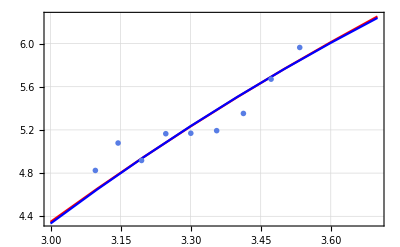

```mathematica
Show[
{ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553g100g⟦1⟧],100,i553g100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Red,PlotTheme->"Detailed"],
ListLinePlot[Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553g10g⟦1⟧],10,i553g10g⟦2⟧,2,2]},{x,3.0,3.7,0.1}],PlotStyle->Blue,PlotTheme->"Detailed"],
ListPlot[lnKIEi553gR,PlotTheme->"Business"]}
]
```

### Combined figure 2

```mathematica
lnKIEgWTtable=Table[{x,Log@KIEg[1000/x,Δ,λ,R0[WTg100⟦1⟧],100,WTg100⟦2⟧,2,2]},{x,3.0,3.7,0.1}];
lnKIEgi553vtable=Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553v100g⟦1⟧],100,i553v100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}];
lnKIEgi553ltable=Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553l100g⟦1⟧],100,i553l100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}];
lnKIEgi553atable=Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553a100g⟦1⟧],100,i553a100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}];
lnKIEgi553gtable=Table[{x,Log@KIEg[1000/x,Δ,λ,R0[i553g100g⟦1⟧],100,i553g100g⟦2⟧,2,2]},{x,3.0,3.7,0.1}];
```

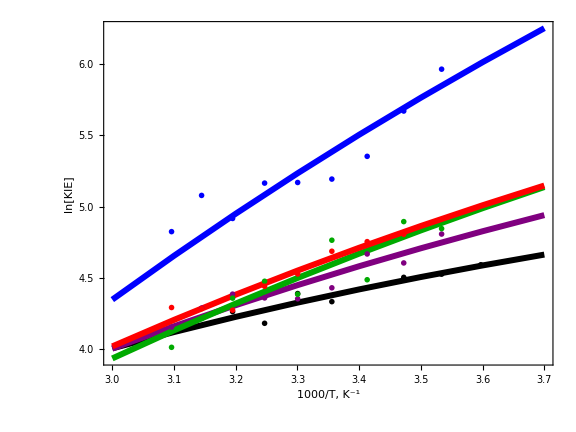

```mathematica
Figure4=Show[
ListLinePlot[{lnKIEgWTtable,lnKIEgi553vtable,lnKIEgi553ltable,lnKIEgi553atable,lnKIEgi553gtable},
Axes->False,Frame->True,PlotRange->All,
FrameLabel->{"1000/T, K^-1","ln[KIE]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->{
{Black,Thickness[0.0075]},
{Purple,Thickness[0.0075]},
{Darker[Green], Thickness[0.0075]},
{Red,Thickness[0.0075]},
{Blue,Thickness[0.0075]}
},
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,FrameTicks->{{{{4.0,"4.0",{0.02,0}},{4.5,"4.5",{0.02,0}},{5.0,"5.0",{0.02,0}},{5.5,"5.5",{0.02,0}},{6.0,"6.0",{0.02,0}}},None},{{{3.0,"3.0",{0.02,0}},{3.1,"3.1",{0.02,0}},{3.2,"3.2",{0.02,0}},{3.3,"3.3",{0.02,0}},{3.4,"3.4",{0.02,0}},{3.5,"3.5",{0.02,0}},{3.6,"3.6",{0.02,0}},{3.7,"3.7",{0.02,0}}},None}}
],
ListPlot[{lnKIEWTR,lnKIEi553vR,lnKIEi553lR,lnKIEi553aR,lnKIEi553gR},PlotTheme->"OpenMarkersThick",PlotStyle->{Black,Purple,Darker[Green],Red,Blue}]
]
```

```mathematica
Export["Figure4.tif",Figure4,ImageResolution->600]
```

Figure4.tif

```mathematica
Export["Figure4.eps",Figure4,ImageResolution->600]
```

Figure4.eps

```mathematica
Export["Figure4.pdf",Figure4,ImageResolution->600]
```

Figure4.pdf

### The table with parameters

```mathematica
{WTg100,i553v100g,i553l100g,i553a100g,i553g100g}//TableForm
```

2.77 | 132.832
2.894 | 105.462
3.002 | 92.8099
2.973 | 96.3405
3.242 | 81.978

```mathematica
{WTg10,i553v10g,i553l10g,i553a10g,i553g10g}//TableForm
```

2.881 | 368.156
2.997 | 316.332
3.104 | 266.419
3.075 | 295.112
3.351 | 257.538

## Parameter ranges for the double mutant (SLO DM)

```mathematica
λDM=45.6;
MDM=100;
ReqWT=WTg100⟦1⟧;
μmax=2;νmax=2;
RDAtable=Table[ReqWT+i 0.02,{i,0,8}];
colorTable=Table[RGBColor[i 0.1,0,0],{i,0,8}];
TT=303;
start=100;finish=300;step=20;
Monitor[
listFig5=Table[
Table[{Ω,KIEg[TT,Δ,λDM,R0[Ri],MDM,Ω,μmax,νmax]},{Ω,start,finish,step}],
{Ri,RDAtable}
],
Grid[{
{ProgressIndicator[Dynamic[Ω],{start,finish}],"\nΩ"->Ω"cm^-1"},
{ProgressIndicator[Dynamic[Ri],{ReqWT,ReqWT+0.2}],"\nR_DA"->Ri"Å"}
},Alignment->{{Right,Left},{Bottom,Bottom}},Spacings->{1,-0.5}]
];
```

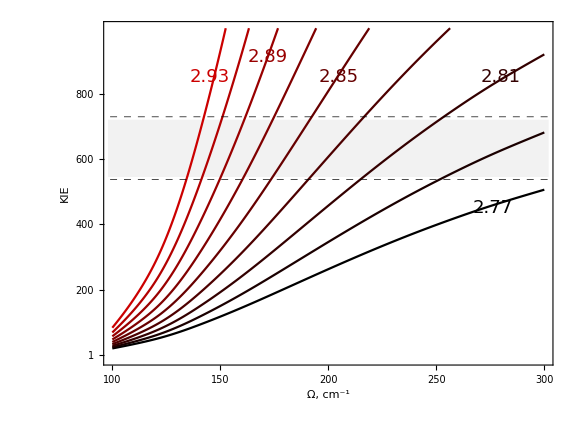

```mathematica
Figure5=ListLinePlot[listFig5,
FrameStyle->Thickness[0.002],
GridLines->{None,{537,729}},
GridLinesStyle->Directive[Black,Dashed],
PlotRange->{-10,1000},
BaseStyle->{FontFamily->"Helvetica",FontSize->24},
PlotStyle->colorTable,
Frame->True,Axes->False,
ImageSize->Large,AspectRatio->0.75,
FrameStyle->Thickness[0.005],
FrameTicksStyle->Black,
LabelStyle->Black,
FrameLabel->{"Ω, cm^-1","KIE"},
FrameTicks->{{{{1,"1"},{200,"200",{0.02,0}},{400,"400",{0.02,0}},{600,"600",{0.02,0}},{800,"800",{0.02,0}}},None},{{{100,"100",{0.02,0}},{150,"150",{0.02,0}},{200,"200",{0.02,0}},{250,"250",{0.02,0}},{300,"300",{0.02,0}}},None}},
Prolog->{RGBColor[0.95,0.95,0.95],Rectangle[{98,545},{302,720}]},
Epilog->{
Text[Style["2.93",FontSize->18,FontColor->RGBColor[0.8,0,0]],{145,850},{0,0},Background->White],
Text[Style["2.89",FontSize->18,FontColor->RGBColor[0.6,0,0]],{172,912},{0,0},Background->White],
Text[Style["2.85",FontSize->18,FontColor->RGBColor[0.4,0,0]],{205,850},{0,0},Background->White],
Text[Style["2.81",FontSize->18,FontColor->RGBColor[0.2,0,0]],{280,850},{0,0},Background->White],
Text[Style["2.77",FontSize->18,FontColor->RGBColor[0.0,0,0]],{276,450},{0,0},Background->White]
},
InterpolationOrder->3]
```

```mathematica
Export["Figure5-final.tif",Figure5,ImageResolution->600]
```

Figure5-final.tif

```mathematica
Export["Figure5-final.eps",Figure5,ImageResolution->600]
```

Figure5-final.eps

```mathematica
Export["Figure5-final.pdf",Figure5,ImageResolution->600]
```

Figure5-final.pdf